## Generating moment function (+) and its inverse. It takes the form G0=f(s)/g(s) and f(s) is analytic for any complex s. The poles of G0 are given by g(s0)=0.

```mathematica
G0[s_,r1_,r2_,k_]:=((s+r1)(s+r2))/(r1(s+r2)+s(s+r2)Cosh[k Sqrt[s+r1]]+s Sqrt[(s+r1)]Sqrt[(s+r2)]Sinh[k Sqrt[s+r1]])
G0Inverse[s_,r1_,r2_]:=FullSimplify[1/G0[s,r1,r2,1]]
PoleFunction[s_,r1_,r2_]:=r1(s+r2)+s(s+r2)Cosh[Sqrt[s+r1]]+s Sqrt[(s+r1)]Sqrt[(s+r2)]Sinh[Sqrt[s+r1]]
```

### Real part of G0 and its inverse varying r1 (r+) and r2 (r-). Here, G0 is the generating moment function if the target is at +xt. The vertical line indicates the asymptote at r2, where for any r1, r2, Re[G0]→-∞.

```mathematica
Manipulate[GraphicsRow[{Plot[G0Inverse[s,r1,r2],{s,-10,10},PlotRange-> {{-5,5},{-10,10}},PlotLabel->"G0Inverse",Epilog->{Line[{{-r2,-10},{-r2,10}}]}],Plot[G0[s,r1,r2,1],{s,-10,10},PlotRange-> {{-5,5},{-10,10}},PlotLabel->"G0",Epilog->{Line[{{-r2,-10},{-r2,10}}]}]}],{{r1,1},0.1,5},{{r2,1},0.1,5}]
```

### Let’s suppose that s only takes real values. Then, the first derivative of G0Inverse is always positive. Thus, we find a single root s0 of G0Inverse (or pole of G0 if G0(s0)≠ ∞ ) between (-r2,∞). If s0 is a pole, there is no doubt that is order 1 because the first derivative never vanishes since it’s always positive.

```mathematica
FullSimplify[D[G0Inverse[s,r1,r2],s]]
```

(-2 r1 (r2+s)^(3/2)+(r2+s) (s^2+r1 (s+2 √(r2+s))) Cosh[√(r1+s)]+√(r1+s) (r1 (2 r2+s)+s (r2+r2 √(r2+s)+s √(r2+s))) Sinh[√(r1+s)])/(2 (r1+s)^2 (r2+s)^(3/2))

```mathematica
Manipulate[Plot[(-2 r1 (r2+s)^(3/2)+(r2+s) (s^2+r1 (s+2 √(r2+s))) Cosh[√(r1+s)]+√(r1+s) (r1 (2 r2+s)+s (r2+r2 √(r2+s)+s √(r2+s))) Sinh[√(r1+s)])/(2 (r1+s)^2 (r2+s)^(3/2)),{s,-10,10},Epilog->{Line[{{-r2,-10},{-r2,10}}]},PlotRange->{{-10,10},{0,5}},PlotLabel->"∂_s G0Inverse"],{{r1,1},0.01,5},{{r2,1},0.01,5}]
```

### We found that there is a single real pole but, are there more poles? Concretely, we are interested in those poles that can have a real part larger than the real pole, since the largest real one domains the large time behaviour.

```mathematica
Manipulate[GraphicsRow[{Plot[Re[G0Inverse[s+k ⅈ,r1,r2]],{s,-10,0},Epilog->{Line[{{-r2,-10},{-r2,10}}]},PlotRange->{{-10,0},{-5,5}},PlotLabel->"Re[G0Inverse]"],Plot[Im[G0Inverse[s+k ⅈ,r1,r2]],{s,-10,0},PlotLabel->"Im[G0Inverse]",Epilog->{Line[{{-r2,-10},{-r2,10}}]},PlotRange->{{-10,0},{-5,5}}]}],{{k,0},0,5},{{r1,1},0.1,5},{{r2,1},0.1,5}]
```

### It seems that G0Inverse does not have any complex pole, as the imaginary part does not vanish for any s = a + ⅈ b, where b ≠ 0.

### All the analysis is also valid when the target is at -xt. In this case, G_(0,-)(r1,r2)=G_(0,+)(r2,r1).

## Finding numerically the largest real pole

```mathematica
G0Inverse[s,r1,r2]
```

r1/(r1+s)+(s Cosh[√(r1+s)])/(r1+s)+(s Sinh[√(r1+s)])/(√(r1+s) √(r2+s))

```mathematica
FindRoot[(r1+s Cosh[√(r1+s)])/(r1+s)+(s Sinh[√(r1+s)])/(√(r1+s) √(r2+s))==0,{s,0}]
```

```mathematica
Manipulate[GraphicsRow[{Plot[{G0Inverse[s,r1,r2],r1(s+r2)+s(s+r2)Cosh[Sqrt[s+r1]]+s Sqrt[(s+r1)]Sqrt[(s+r2)]Sinh[Sqrt[s+r1]]},{s,-10,0},PlotLabel->"G_(0, +)",Epilog->{Line[{{-r2,-10},{-r2,10}}]},PlotRange->{{-10,0},{-5,5}}],Plot[{G0Inverse[s,r2,r1],r2(s+r1)+s(s+r1)Cosh[Sqrt[s+r2]]+s Sqrt[(s+r2)]Sqrt[(s+r1)]Sinh[Sqrt[s+r2]]},{s,-10,0},PlotLabel->"G_(0, -)",Epilog->{Line[{{-r1,-10},{-r1,10}}]},PlotRange->{{-10,0},{-5,5}}]}],{{r1,1},0.1,5},{{r2,1},0.1,5}]
```

```mathematica
FindRoot[PoleFunction[s,r1,r2]==0,{s,0}]
```

```mathematica
Manipulate[Row[{FindRoot[PoleFunction[s,r1,r2]==0,{s,-0.3,-r2+0.01,0}],FindRoot[PoleFunction[s,r2,r1]==0,{s,-0.3,-r1+0.01,0}]}],{{r1,1.8},0.1,5},{{r2,0.5},0.1,5}]
```

```mathematica
Manipulate[Row[{FindRoot[G0Inverse[s,r1,r2]==0,{s,0}],FindRoot[G0Inverse[s,r2,r1]==0,{s,0}]}],{{r1,r1},0.1,5},{{r2,r2},0.1,5}]
```

### Calculating the root of 1/G_(0,+) and 1/G_(0,-) and their residues. Since they are of order 1, it is easy computable using the first derivative → Res[G_(0,+);s0]=1/G_(0,+)'(s0).

```mathematica
r1=1;r2=2;Pol1=s/.FindRoot[G0Inverse[s,r1,r2]==0,{s,0}];Pol2=s/.FindRoot[G0Inverse[s,r2,r1]==0,{s,0}];
Res1=Series[G0Inverse[s,r1,r2],{s,Pol1,3}]
Res2=Series[G0Inverse[s,r2,r1],{s,Pol2,3}]
```

0.609157 (s+0.697453)+2.37531 (s+0.697453)^2+1.20325 (s+0.697453)^3+O[s+0.697453]^4

2.46505 (s+0.438809)+4.20441 (s+0.438809)^2+1.1752 (s+0.438809)^3+O[s+0.438809]^4

### The inverse laplace transform when t→∞ is

```mathematica
(p (Pol1+r1)(Pol1+r2))/SeriesCoefficient[G0Inverse[s,r1,r2],{s,Pol1,1}] Exp[Pol1 t]+((1-p)(Pol2+r1)(Pol2+r2))/SeriesCoefficient[G0Inverse[s,r2,r1],{s,Pol2,1}] Exp[Pol2 t]
```

0.517544 ⅇ^(-0.697453 t)+0.071084 ⅇ^(-0.438809 t)

## Cross time of both behaviour given by the exponentials of the poles

```mathematica
F1Plus[x_,y_]:=1/x^2(Cosh[x]+x/y Sinh[x]-1);
F1Minus[x_,y_]:=F1Plus[y,x];
F1Total[x_,y_,p_]:=p F1Plus[x,y]+(1-p)F1Minus[x,y];
```

```mathematica
TableMFTP=Table[{p,FindMinimum[{FullSimplify[Limit[F1Total[γ1,γ2,pvar],{pvar->p}]],γ1>=0,γ2>=0},{{γ1,1},{γ2,1}}]},{p,0,1,0.001}];
```

$Aborted

```mathematica
TableMFTP={{0.,{0.5007727992052545,{γ1->1294.0737338038875,γ2->0.0010468801548235318}}},{0.001,{0.7474729261833204,{γ1->5.434415104979251,γ2->0.5225728691861948}}},{0.002,{0.7810805669311874,{γ1->4.93866498075973,γ2->0.5676354526759761}}},{0.003,{0.8044786672539047,{γ1->4.655948734906241,γ2->0.5973111673540118}}},{0.004,{0.8231033751037483,{γ1->4.458895414001649,γ2->0.6200779342097023}}},{0.005,{0.8388648229333984,{γ1->4.308179832196306,γ2->0.6388167957901274}}},{0.006,{0.8526833676396675,{γ1->4.18647181790016,γ2->0.6548836376520331}}},{0.007,{0.8650810553225532,{γ1->4.084606401971805,γ2->0.6690332936305231}}},{0.008,{0.8763857952144976,{γ1->3.99715300726246,γ2->0.6817324954624407}}},{0.009000000000000001,{0.8868185672209301,{γ1->3.9206313757725297,γ2->0.6932915094873033}}},{0.01,{0.8965361850620971,{γ1->3.852678959696756,γ2->0.7039278544342055}}},{0.011,{0.9056544242632428,{γ1->3.7916195320547326,γ2->0.7138003760033553}}},{0.012,{0.9142614858075051,{γ1->3.736221438579531,γ2->0.7230288831392745}}},{0.013000000000000001,{0.9224262975437845,{γ1->3.685553567988887,γ2->0.7317061454223058}}},{0.014,{0.9302038748816722,{γ1->3.6388952090729485,γ2->0.7399055758954216}}},{0.015,{0.9376389167464982,{γ1->3.5956773001379005,γ2->0.7476863449866015}}},{0.016,{0.9447682958966257,{γ1->3.555442815497462,γ2->0.7550968966550111}}},{0.017,{0.9516228309677638,{γ1->3.517819272303758,γ2->0.7621774335656932}}},{0.018000000000000002,{0.9582285772211739,{γ1->3.482499168279945,γ2->0.7689617158192457}}},{0.019,{0.9646077860399384,{γ1->3.449225757444221,γ2->0.7754783900594061}}},{0.02,{0.9707796310492407,{γ1->3.4177825082354287,γ2->0.7817519895901204}}},{0.021,{0.9767607663950151,{γ1->3.387985157686801,γ2->0.7878036991569046}}},{0.022,{0.9825657620841534,{γ1->3.359675631414555,γ2->0.7936519482345837}}},{0.023,{0.9882074477913045,{γ1->3.332717327918157,γ2->0.7993128772543131}}},{0.024,{0.9936971875045015,{γ1->3.306991416085435,γ2->0.8048007082751273}}},{0.025,{0.9990451012134848,{γ1->3.2823938957903684,γ2->0.8101280428167458}}},{0.026000000000000002,{1.004260245554571,{γ1->3.258833240593615,γ2->0.8153061034842967}}},{0.027,{1.0093507622923086,{γ1->3.236228489688002,γ2->0.8203449317298361}}},{0.028,{1.0143240013402957,{γ1->3.2145076902784906,γ2->0.8252535510306825}}},{0.029,{1.0191866234381854,{γ1->3.1936066160205345,γ2->0.8300401025425135}}},{0.03,{1.0239446864330901,{γ1->3.173467704909482,γ2->0.834711958652594}}},{0.031,{1.0286037182416707,{γ1->3.154039173094504,γ2->0.8392758186452216}}},{0.032,{1.0331687789116655,{γ1->3.1352742708296257,γ2->0.8437377897795864}}},{0.033,{1.0376445137006969,{γ1->3.117130654101965,γ2->0.8481034563879157}}},{0.034,{1.0420351987050238,{γ1->3.0995698510446785,γ2->0.8523779390711799}}},{0.035,{1.0463447802720953,{γ1->3.082556806510725,γ2->0.8565659456592671}}},{0.036000000000000004,{1.0505769091970865,{γ1->3.0660594914845296,γ2->0.8606718152826194}}},{0.037,{1.054734970519376,{γ1->3.0500485665818102,γ2->0.8646995566509704}}},{0.038,{1.0588221095887427,{γ1->3.034497090908589,γ2->0.8686528814357133}}},{0.039,{1.0628412549541602,{γ1->3.0193802691489573,γ2->0.8725352334939827}}},{0.04,{1.0667951385340837,{γ1->3.004675231023797,γ2->0.8763498145452407}}},{0.041,{1.0706863134510327,{γ1->2.990360838282432,γ2->0.8800996068084723}}},{0.042,{1.0745171698513576,{γ1->2.976417515211219,γ2->0.8837873930248035}}},{0.043000000000000003,{1.0782899489804132,{γ1->2.96282709930935,γ2->0.8874157742223197}}},{0.044,{1.0820067557416668,{γ1->2.949572709325144,γ2->0.8909871855240233}}},{0.045,{1.0856695699338461,{γ1->2.936638628290906,γ2->0.8945039102538987}}},{0.046,{1.0892802563315884,{γ1->2.924010199560459,γ2->0.8979680925578727}}},{0.047,{1.0928405737512303,{γ1->2.9116737341562433,γ2->0.9013817487248428}}},{0.048,{1.0963521832233507,{γ1->2.899616427984174,γ2->0.9047467773663096}}},{0.049,{1.0998166553769069,{γ1->2.887826287684202,γ2->0.9080649685910335}}},{0.05,{1.1032354771255894,{γ1->2.876292064060022,γ2->0.9113380122923113}}},{0.051000000000000004,{1.1066100577350013,{γ1->2.8650031921789934,γ2->0.9145675056496968}}},{0.052000000000000005,{1.109941734339055,{γ1->2.8539497373577962,γ2->0.9177549599335101}}},{0.053,{1.1132317769652411,{γ1->2.843122346354783,γ2->0.920901806689045}}},{0.054,{1.1164813931209645,{γ1->2.8325122031795122,γ2->0.924009403367653}}},{0.055,{1.1196917319867286,{γ1->2.8221109890062572,γ2->0.9270790384634394}}},{0.056,{1.1228638882564281,{γ1->2.8119108457435225,γ2->0.9301119362071628}}},{0.057,{1.1259989056602464,{γ1->2.801904342867562,γ2->0.9331092608627277}}},{0.058,{1.1290977802015059,{γ1->2.792084447175964,γ2->0.9360721206662609}}},{0.059000000000000004,{1.1321614631352588,{γ1->2.7824444951588547,γ2->0.9390015714431346}}},{0.06,{1.135190863713262,{γ1->2.7729781677211816,γ2->0.9418986199342864}}},{0.061,{1.138186851717261,{γ1->2.763679467020578,γ2->0.9447642268596403}}},{0.062,{1.1411502598001328,{γ1->2.7545426952123315,γ2->0.9475993097433333}}},{0.063,{1.1440818856523274,{γ1->2.745562434916582,γ2->0.9504047455228525}}},{0.064,{1.1469824940092306,{γ1->2.736733531243341,γ2->0.9531813729617383}}},{0.065,{1.149852818513439,{γ1->2.7280510752289713,γ2->0.9559299948834853}}},{0.066,{1.1526935634445161,{γ1->2.7195103885534966,γ2->0.9586513802424202}}},{0.067,{1.1555054053275327,{γ1->2.7111070094220295,γ2->0.9613462660457696}}},{0.068,{1.1582889944305785,{γ1->2.702836679505736,γ2->0.9640153591396301}}},{0.069,{1.1610449561604368,{γ1->2.6946953318486067,γ2->0.96665933787036}}},{0.07,{1.1637738923647245,{γ1->2.6866790796557667,γ2->0.9692788536317439}}},{0.07100000000000001,{1.1664763825480313,{γ1->2.6787842058875415,γ2->0.9718745323073176}}},{0.07200000000000001,{1.1691529850088622,{γ1->2.6710071535909297,γ2->0.9744469756163069}}},{0.073,{1.171804237903587,{γ1->2.6633445169068386,γ2->0.9769967623708972}}},{0.074,{1.174430660243012,{γ1->2.6557930326973196,γ2->0.9795244496517856}}},{0.075,{1.1770327528267095,{γ1->2.648349572742341,γ2->0.9820305739083616}}},{0.076,{1.179610999119771,{γ1->2.641011136460393,γ2->0.9845156519893129}}},{0.077,{1.1821658660762435,{γ1->2.633774844111309,γ2->0.9869801821088565}}},{0.078,{1.1846978049131516,{γ1->2.6266379304436884,γ2->0.9894246447534647}}},{0.079,{1.1872072518386674,{γ1->2.6195977387524887,γ2->0.9918495035334317}}},{0.08,{1.1896946287376913,{γ1->2.61265171531552,γ2->0.9942552059832752}}},{0.081,{1.1921603438178472,{γ1->2.605797404180299,γ2->0.9966421843146853}}},{0.082,{1.1946047922186303,{γ1->2.5990324422751927,γ2->0.9990108561253732}}},{0.083,{1.197028356586242,{γ1->2.5923545548209774,γ2->1.0013616250668655}}},{0.084,{1.1994314076164425,{γ1->2.5857615510210383,γ2->1.0036948814741635}}},{0.085,{1.2018143045675476,{γ1->2.5792513200101665,γ2->1.0060110029598153}}},{0.08600000000000001,{1.2041773957455633,{γ1->2.572821827043618,γ2->1.008310354974818}}},{0.08700000000000001,{1.2065210189632674,{γ1->2.5664711099095907,γ2->1.0105932913385829}}},{0.088,{1.208845501974929,{γ1->2.560197275549619,γ2->1.0128601547399894}}},{0.089,{1.2111511628882181,{γ1->2.5539984968726426,γ2->1.0151112772114232}}},{0.09,{1.2134383105547526,{γ1->2.5478730097496034,γ2->1.017346980577538}}},{0.091,{1.2157072449406119,{γ1->2.541819110176483,γ2->1.0195675768803512}}},{0.092,{1.217958257478059,{γ1->2.535835151594604,γ2->1.0217733687821833}}},{0.093,{1.2201916313996155,{γ1->2.529919542357882,γ2->1.023964649947805}}},{0.094,{1.2224076420555607,{γ1->2.5240707433374787,γ2->1.0261417054070854}}},{0.095,{1.224606557215845,{γ1->2.5182872656550543,γ2->1.028304811899337}}},{0.096,{1.2267886373573351,{γ1->2.5125676685364224,γ2->1.0304542382004542}}},{0.097,{1.2289541359372589,{γ1->2.5069105572780552,γ2->1.0325902454338853}}},{0.098,{1.2311032996536415,{γ1->2.501314581319408,γ2->1.0347130873663881}}},{0.099,{1.2332363686934837,{γ1->2.495778432414531,γ2->1.036823010689465}}},{0.1,{1.2353535769693775,{γ1->2.4903008428969304,γ2->1.0389202552873062}}},{0.101,{1.2374551523452055,{γ1->2.4848805840320405,γ2->1.041005054492021}}},{0.10200000000000001,{1.2395413168515375,{γ1->2.479516464452053,γ2->1.0430776353268738}}},{0.10300000000000001,{1.2416122868912842,{γ1->2.474207328668251,γ2->1.0451382187382021}}},{0.10400000000000001,{1.243668273436151,{γ1->2.468952055656277,γ2->1.0471870198166509}}},{0.105,{1.245709482214373,{γ1->2.463749557510125,γ2->1.0492242480083191}}},{0.106,{1.2477361138902157,{γ1->2.4585987781608685,γ2->1.051250107316347}}},{0.107,{1.2497483642356626,{γ1->2.453498692156469,γ2->1.0532647964934956}}},{0.108,{1.2517464242947063,{γ1->2.448448303499187,γ2->1.0552685092261704}}},{0.109,{1.253730480540634,{γ1->2.443446644537394,γ2->1.0572614343103746}}},{0.11,{1.255700715026654,{γ1->2.4384927749087475,γ2->1.0592437558199856}}},{0.111,{1.2576573055302165,{γ1->2.4335857805319243,γ2->1.0612156532677823}}},{0.112,{1.2596004256913433,{γ1->2.428724772644265,γ2->1.063177301759585}}},{0.113,{1.2615302451452606,{γ1->2.42390888688284,γ2->1.0651288721418677}}},{0.114,{1.2634469296496311,{γ1->2.4191372824066244,γ2->1.0670705311431603}}},{0.115,{1.265350641206639,{γ1->2.414409141057604,γ2->1.0690024415095827}}},{0.116,{1.267241538180186,{γ1->2.40972366655875,γ2->1.0709247621347684}}},{0.117,{1.2691197754084325,{γ1->2.4050800837469595,γ2->1.0728376481844824}}},{0.11800000000000001,{1.2709855043119096,{γ1->2.400477637839143,γ2->1.0747412512161865}}},{0.11900000000000001,{1.2728388729974116,{γ1->2.3959155937297565,γ2->1.0766357192937874}}},{0.12,{1.274680026357863,{γ1->2.391393235318199,γ2->1.0785211970978186}}},{0.121,{1.2765091061683604,{γ1->2.386909864864545,γ2->1.0803978260312628}}},{0.122,{1.278326251178553,{γ1->2.3824648023722084,γ2->1.082265744321213}}},{0.123,{1.2801315972015395,{γ1->2.3780573849962114,γ2->1.0841250871166}}},{0.124,{1.281925277199438,{γ1->2.3736869664757805,γ2->1.085975986582136}}},{0.125,{1.2837074213657782,{γ1->2.3693529165900893,γ2->1.087818571988663}}},{0.126,{1.2854781572048561,{γ1->2.3650546206360388,γ2->1.089652969800075}}},{0.127,{1.2872376096081968,{γ1->2.3607914789269953,γ2->1.0914793037569686}}},{0.128,{1.2889859009282392,{γ1->2.3565629063115177,γ2->1.0932976949571698}}},{0.129,{1.2907231510493746,{γ1->2.3523683317112725,γ2->1.0951082619337407}}},{0.13,{1.2924494774564523,{γ1->2.3482071976761967,γ2->1.09691112072775}}},{0.131,{1.2941649953008554,{γ1->2.3440789599586997,γ2->1.0987063849631238}}},{0.132,{1.2958698174642598,{γ1->2.3399830871026697,γ2->1.100494165914076}}},{0.133,{1.2975640546201717,{γ1->2.335919060049007,γ2->1.1022745725724377}}},{0.134,{1.2992478152933313,{γ1->2.331886371756045,γ2->1.1040477117121439}}},{0.135,{1.3009212059170823,{γ1->2.327884526834296,γ2->1.1058136879514235}}},{0.136,{1.3025843308887823,{γ1->2.3239130411949,γ2->1.1075726038128073}}},{0.137,{1.3042372926233432,{γ1->2.319971441711156,γ2->1.1093245597810395}}},{0.138,{1.3058801916049703,{γ1->2.3160592658925707,γ2->1.111069654358993}}},{0.139,{1.3075131264371802,{γ1->2.3121760615708546,γ2->1.1128079841216476}}},{0.14,{1.3091361938911612,{γ1->2.308321386597369,γ2->1.1145396437682398}}},{0.14100000000000001,{1.3107494889525466,{γ1->2.3044948085515085,γ2->1.1162647261726388}}},{0.14200000000000002,{1.3123531048666643,{γ1->2.3006959044595603,γ2->1.117983322432026}}},{0.14300000000000002,{1.3139471331823158,{γ1->2.2969242605235927,γ2->1.1196955219139555}}},{0.14400000000000002,{1.3155316637941545,{γ1->2.2931794718599487,γ2->1.1214014123018483}}},{0.145,{1.3171067849837057,{γ1->2.289461142246921,γ2->1.123101079638985}}},{0.146,{1.3186725834590896,{γ1->2.285768883881269,γ2->1.124794608371068}}},{0.147,{1.320229144393491,{γ1->2.2821023171431567,γ2->1.1264820813873897}}},{0.148,{1.3217765514624271,{γ1->2.278461070369214,γ2->1.1281635800606868}}},{0.149,{1.3233148868798603,{γ1->2.2748447796333497,γ2->1.1298391842857038}}},{0.15,{1.3248442314331919,{γ1->2.27125308853503,γ2->1.1315089725165366}}},{0.151,{1.3263646645171887,{γ1->2.267685647994698,γ2->1.1331730218027931}}},{0.152,{1.3278762641668735,{γ1->2.264142116056063,γ2->1.1348314078246164}}},{0.153,{1.3293791070894252,{γ1->2.260622157694989,γ2->1.1364842049266213}}},{0.154,{1.3308732686951155,{γ1->2.257125444634695,γ2->1.1381314861507708}}},{0.155,{1.3323588231273287,{γ1->2.253651655167056,γ2->1.1397733232682494}}},{0.156,{1.3338358432916873,{γ1->2.2502004739797314,γ2->1.141409786810348}}},{0.157,{1.3353044008843196,{γ1->2.246771591988921,γ2->1.1430409460984297}}},{0.158,{1.3367645664193046,{γ1->2.243364706177515,γ2->1.1446668692729693}}},{0.159,{1.3382164092553155,{γ1->2.239979519438433,γ2->1.1462876233217358}}},{0.16,{1.3396599976214931,{γ1->2.2366157404229705,γ2->1.1479032741071329}}},{0.161,{1.341095398642579,{γ1->2.2332730833939323,γ2->1.1495138863927212}}},{0.162,{1.3425226783633284,{γ1->2.2299512680834024,γ2->1.1511195238689669}}},{0.163,{1.343941901772236,{γ1->2.226650019554968,γ2->1.1527202491782387}}},{0.164,{1.3453531328245876,{γ1->2.223369068070213,γ2->1.1543161239390691}}},{0.165,{1.3467564344648704,{γ1->2.2201081489593575,γ2->1.1559072087697233}}},{0.166,{1.3481518686485576,{γ1->2.216867002495859,γ2->1.157493563311086}}},{0.167,{1.3495394963632916,{γ1->2.213645373774853,γ2->1.1590752462488967}}},{0.168,{1.3509193776494832,{γ1->2.210443012595276,γ2->1.1606523153353525}}},{0.169,{1.3522915716203499,{γ1->2.207259673345557,γ2->1.1622248274101037}}},{0.17,{1.3536561364814086,{γ1->2.204095114892731,γ2->1.163792838420662}}},{0.171,{1.3550131295494419,{γ1->2.2009491004748614,γ2->1.1653564034422303}}},{0.17200000000000001,{1.3563626072709556,{γ1->2.197821397596658,γ2->1.1669155766969994}}},{0.17300000000000001,{1.3577046252401432,{γ1->2.19471177792817,γ2->1.1684704115728988}}},{0.17400000000000002,{1.3590392382163756,{γ1->2.1916200172064446,γ2->1.170020960641838}}},{0.17500000000000002,{1.3603665001412248,{γ1->2.1885458951400643,γ2->1.1715672756774587}}},{0.176,{1.3616864641550481,{γ1->2.185489195316437,γ2->1.1731094076723931}}},{0.177,{1.3629991826131316,{γ1->2.182449705111769,γ2->1.1746474068550727}}},{0.178,{1.3643047071014238,{γ1->2.1794272156036145,γ2->1.1761813227060718}}},{0.179,{1.3656030884518546,{γ1->2.1764215214859153,γ2->1.177711203974032}}},{0.18,{1.3668943767572712,{γ1->2.1734324209864546,γ2->1.179237098691153}}},{0.181,{1.3681786213859835,{γ1->2.170459715786626,γ2->1.1807590541882784}}},{0.182,{1.3694558709959486,{γ1->2.167503210943469,γ2->1.1822771171095954}}},{0.183,{1.3707261735485923,{γ1->2.1645627148138593,γ2->1.1837913334269423}}},{0.184,{1.3719895763222878,{γ1->2.161638038980819,γ2->1.1853017484537505}}},{0.185,{1.3732461259254958,{γ1->2.158728998181838,γ2->1.1868084068586242}}},{0.186,{1.374495868309579,{γ1->2.155835410239184,γ2->1.1883113526785773}}},{0.187,{1.3757388487813036,{γ1->2.1529570959920994,γ2->1.1898106293319375}}},{0.188,{1.3769751120150284,{γ1->2.1500938792308397,γ2->1.1913062796309044}}},{0.189,{1.378204702064601,{γ1->2.1472455866325006,γ2->1.1927983457938207}}},{0.19,{1.3794276623749648,{γ1->2.1444120476985558,γ2->1.194286869457109}}},{0.191,{1.380644035793483,{γ1->2.141593094694076,γ2->1.1957718916869304}}},{0.192,{1.3818538645809924,{γ1->2.138788562588553,γ2->1.1972534529905436}}},{0.193,{1.3830571904225957,{γ1->2.1359982889982954,γ2->1.198731593327391}}},{0.194,{1.3842540544381914,{γ1->2.1332221141303322,γ2->1.2002063521199062}}},{0.195,{1.3854444971927586,{γ1->2.130459880727795,γ2->1.2016777682640678}}},{0.196,{1.3866285587064018,{γ1->2.127711434016705,γ2->1.2031458801396853}}},{0.197,{1.3878062784641536,{γ1->2.124976621654158,γ2->1.2046107256204477}}},{0.198,{1.3889776954255582,{γ1->2.1222552936778305,γ2->1.2060723420837283}}},{0.199,{1.3901428480340234,{γ1->2.119547302456783,γ2->1.20753076642015}}},{0.2,{1.3913017742259661,{γ1->2.116852502643519,γ2->1.2089860350429233}}},{0.201,{1.3924545114397409,{γ1->2.114170751127274,γ2->1.2104381838969844}}},{0.202,{1.3936010966243693,{γ1->2.1115019069884546,γ2->1.211887248467886}}},{0.203,{1.3947415662480684,{γ1->2.108845831454252,γ2->1.2133332637905003}}},{0.20400000000000001,{1.3958759563065877,{γ1->2.1062023878553533,γ2->1.2147762644575226}}},{0.20500000000000002,{1.397004302331358,{γ1->2.103571441583726,γ2->1.2162162846277638}}},{0.20600000000000002,{1.3981266393974605,{γ1->2.1009528600514584,γ2->1.2176533580342639}}},{0.20700000000000002,{1.3992430021314117,{γ1->2.098346512650604,γ2->1.2190875179922105}}},{0.20800000000000002,{1.4003534247187859,{γ1->2.095752270714023,γ2->1.2205187974066904}}},{0.209,{1.4014579409116599,{γ1->2.0931700074771658,γ2->1.221947228780247}}},{0.21,{1.4025565840358991,{γ1->2.0905995980407956,γ2->1.2233728442202836}}},{0.211,{1.403649386998286,{γ1->2.0880409193346106,γ2->1.2247956754462914}}},{0.212,{1.4047363822934886,{γ1->2.085493850081736,γ2->1.2262157537969172}}},{0.213,{1.4058176020108828,{γ1->2.0829582707640752,γ2->1.2276331102368794}}},{0.214,{1.4068930778412243,{γ1->2.0804340635884766,γ2->1.2290477753637192}}},{0.215,{1.4079628410831808,{γ1->2.0779211124537134,γ2->1.2304597794144203}}},{0.216,{1.4090269226497216,{γ1->2.075419302918241,γ2->1.2318691522718697}}},{0.217,{1.410085353074374,{γ1->2.072928522168705,γ2->1.2332759234711785}}},{0.218,{1.4111381625173454,{γ1->2.0704486589891955,γ2->1.234680122205875}}},{0.219,{1.4121853807715186,{γ1->2.0679796037312137,γ2->1.2360817773339565}}},{0.22,{1.4132270372683193,{γ1->2.0655212482843357,γ2->1.2374809173838115}}},{0.221,{1.414263161083462,{γ1->2.0630734860475504,γ2->1.2388775705600177}}},{0.222,{1.4152937809425787,{γ1->2.0606362119012647,γ2->1.2402717647490185}}},{0.223,{1.416318925226728,{γ1->2.0582093221799354,γ2->1.2416635275246684}}},{0.224,{1.417338621977792,{γ1->2.0557927146453396,γ2->1.243052886153678}}},{0.225,{1.418352898903764,{γ1->2.0533862884604432,γ2->1.2444398676009358}}},{0.226,{1.4193617833839252,{γ1->2.0509899441638555,γ2->1.2458244985347138}}},{0.227,{1.4203653024739213,{γ1->2.0486035836448666,γ2->1.2472068053317744}}},{0.228,{1.4213634829107298,{γ1->2.046227110119039,γ2->1.2485868140823688}}},{0.229,{1.422356351117534,{γ1->2.0438604281043413,γ2->1.2499645505951302}}},{0.23,{1.4233439332084932,{γ1->2.0415034433978163,γ2->1.2513400404018675}}},{0.231,{1.4243262549934235,{γ1->2.0391560630527605,γ2->1.2527133087622666}}},{0.232,{1.4253033419823804,{γ1->2.0368181953564033,γ2->1.2540843806684854}}},{0.233,{1.4262752193901531,{γ1->2.0344897498080834,γ2->1.255453280849669}}},{0.234,{1.4272419121406723,{γ1->2.0321706370978907,γ2->1.2568200337763609}}},{0.23500000000000001,{1.4282034448713259,{γ1->2.029860769085779,γ2->1.2581846636648375}}},{0.23600000000000002,{1.4291598419371963,{γ1->2.0275600587811273,γ2->1.2595471944813512}}},{0.23700000000000002,{1.4301111274152105,{γ1->2.025268420322744,γ2->1.2609076499462883}}},{0.23800000000000002,{1.4310573251082142,{γ1->2.022985768959292,γ2->1.2622660535382457}}},{0.23900000000000002,{1.431998458548962,{γ1->2.020712021030141,γ2->1.263622428498029}}},{0.24,{1.432934551004037,{γ1->2.0184470939466217,γ2->1.2649767978325712}}},{0.241,{1.4338656254776894,{γ1->2.0161909061736774,γ2->1.2663291843187752}}},{0.242,{1.4347917047156047,{γ1->2.0139433772119024,γ2->1.2676796105072847}}},{0.243,{1.4357128112086017,{γ1->2.0117044275799594,γ2->1.2690280987261762}}},{0.244,{1.4366289671962593,{γ1->2.0094739787973586,γ2->1.2703746710845834}}},{0.245,{1.437540194670472,{γ1->2.007251953367605,γ2->1.27171934947626}}},{0.246,{1.4384465153789432,{γ1->2.0050382747616835,γ2->1.2730621555830577}}},{0.247,{1.4393479508286116,{γ1->2.0028328674018976,γ2->1.2744031108783556}}},{0.248,{1.4402445222890137,{γ1->2.0006356566460264,γ2->1.2757422366304125}}},{0.249,{1.4411362507955816,{γ1->1.9984465687718225,γ2->1.2770795539056696}}},{0.25,{1.4420231571528834,{γ1->1.9962655309618056,γ2->1.278415083571969}}},{0.251,{1.4429052619378036,{γ1->1.99409247128839,γ2->1.2797488463017455}}},{0.252,{1.443782585502662,{γ1->1.9919273186992883,γ2->1.2810808625751235}}},{0.253,{1.4446551479782794,{γ1->1.9897700030032281,γ2->1.2824111526829873}}},{0.254,{1.4455229692769835,{γ1->1.9876204548559426,γ2->1.2837397367299703}}},{0.255,{1.4463860690955672,{γ1->1.985478605746454,γ2->1.2850666346374144}}},{0.256,{1.4472444669181828,{γ1->1.9833443879836123,γ2->1.286391866146249}}},{0.257,{1.4480981820191952,{γ1->1.9812177346829254,γ2->1.2877154508198434}}},{0.258,{1.4489472334659763,{γ1->1.9790985797536225,γ2->1.2890374080467883}}},{0.259,{1.4497916401216524,{γ1->1.9769868578859928,γ2->1.2903577570436369}}},{0.26,{1.4506314206478044,{γ1->1.9748825045389653,γ2->1.2916765168575979}}},{0.261,{1.451466593507115,{γ1->1.972785455927929,γ2->1.2929937063691772}}},{0.262,{1.4522971769659738,{γ1->1.970695649012791,γ2->1.2943093442947722}}},{0.263,{1.4531231890970355,{γ1->1.9686130214862718,γ2->1.2956234491892253}}},{0.264,{1.453944647781733,{γ1->1.9665375117624169,γ2->1.2969360394483258}}},{0.265,{1.454761570712743,{γ1->1.9644690589653362,γ2->1.2982471333112766}}},{0.266,{1.4555739753964176,{γ1->1.9624076029181607,γ2->1.2995567488631115}}},{0.267,{1.45638187915516,{γ1->1.9603530841322012,γ2->1.3008649040370721}}},{0.268,{1.4571852991297767,{γ1->1.9583054437963243,γ2->1.3021716166169481}}},{0.269,{1.4579842522817712,{γ1->1.9562646237665173,γ2->1.303476904239367}}},{0.27,{1.4587787553956113,{γ1->1.9542305665556645,γ2->1.3047807843960615}}},{0.271,{1.4595688250809518,{γ1->1.9522032153235043,γ2->1.306083274436084}}},{0.272,{1.460354477774819,{γ1->1.9501825138667757,γ2->1.3073843915679868}}},{0.273,{1.4611357297437615,{γ1->1.9481684066095566,γ2->1.3086841528619737}}},{0.274,{1.4619125970859612,{γ1->1.9461608385937714,γ2->1.3099825752520018}}},{0.275,{1.462685095733311,{γ1->1.9441597554698848,γ2->1.3112796755378657}}},{0.276,{1.4634532414534538,{γ1->1.9421651034877556,γ2->1.3125754703872294}}},{0.277,{1.464217049851794,{γ1->1.9401768294876707,γ2->1.3138699763376367}}},{0.278,{1.4649765363734666,{γ1->1.9381948808915326,γ2->1.315163209798485}}},{0.279,{1.4657317163052834,{γ1->1.9362192056942196,γ2->1.3164551870529684}}},{0.28,{1.4664826047776363,{γ1->1.9342497524551183,γ2->1.317745924260011}}},{0.281,{1.467229216766377,{γ1->1.9322864702896796,γ2->1.3190354374560411}}},{0.28200000000000003,{1.4679715670946645,{γ1->1.930329308861399,γ2->1.3203237425570016}}},{0.28300000000000003,{1.468709670434777,{γ1->1.9283782183736713,γ2->1.3216108553600605}}},{0.28400000000000003,{1.4694435413099005,{γ1->1.9264331495619207,γ2->1.3228967915454313}}},{0.28500000000000003,{1.4701731940958847,{γ1->1.9244940536858515,γ2->1.32418156667813}}},{0.28600000000000003,{1.4708986430229705,{γ1->1.9225608825218312,γ2->1.325465196209716}}},{0.28700000000000003,{1.4716199021774905,{γ1->1.9206335883554124,γ2->1.3267476954799922}}},{0.28800000000000003,{1.4723369855035409,{γ1->1.9187121239739862,γ2->1.3280290797186909}}},{0.289,{1.473049906804626,{γ1->1.9167964426595603,γ2->1.3293093640471252}}},{0.29,{1.4737586797452797,{γ1->1.9148864981816753,γ2->1.330588563479822}}},{0.291,{1.4744633178526552,{γ1->1.9129822447904286,γ2->1.3318666929261174}}},{0.292,{1.4751638345180922,{γ1->1.911083637209634,γ2->1.333143767191743}}},{0.293,{1.4758602429986643,{γ1->1.909190630630096,γ2->1.3344198009803816}}},{0.294,{1.4765525564186874,{γ1->1.9073031807029925,γ2->1.3356948088951914}}},{0.295,{1.4772407877712235,{γ1->1.905421243533384,γ2->1.3369688054403202}}},{0.296,{1.4779249499195417,{γ1->1.90354477567383,γ2->1.3382418050223954}}},{0.297,{1.4786050555985724,{γ1->1.901673734118104,γ2->1.339513821951974}}},{0.298,{1.4792811174163245,{γ1->1.8998080762950362,γ2->1.3407848704449976}}},{0.299,{1.4799531478552927,{γ1->1.8979477600624446,γ2->1.3420549646242097}}},{0.3,{1.4806211592738325,{γ1->1.8960927437011719,γ2->1.3433241185205522}}},{0.301,{1.481285163907522,{γ1->1.8942429859092291,γ2->1.3445923460745448}}},{0.302,{1.481945173870495,{γ1->1.8923984457960283,γ2->1.345859661137646}}},{0.303,{1.4826012011567617,{γ1->1.8905590828767294,γ2->1.3471260774735978}}},{0.304,{1.4832532576415005,{γ1->1.8887248570666537,γ2->1.348391608759735}}},{0.305,{1.483901355082335,{γ1->1.8868957286758195,γ2->1.3496562685882945}}},{0.306,{1.4845455051205914,{γ1->1.885071658403548,γ2->1.3509200704676971}}},{0.307,{1.4851857192825333,{γ1->1.883252607333172,γ2->1.3521830278238118}}},{0.308,{1.4858220089805803,{γ1->1.8814385369268165,γ2->1.3534451540012}}},{0.309,{1.4864543855145074,{γ1->1.8796294090202827,γ2->1.3547064622643492}}},{0.31,{1.4870828600726256,{γ1->1.877825185818003,γ2->1.3559669657988833}}},{0.311,{1.4877074437329447,{γ1->1.8760258298880856,γ2->1.3572266777127582}}},{0.312,{1.4883281474643186,{γ1->1.8742313041574328,γ2->1.3584856110374415}}},{0.313,{1.4889449821275742,{γ1->1.8724415719069458,γ2->1.3597437787290765}}},{0.314,{1.4895579584766194,{γ1->1.8706565967668005,γ2->1.3610011936696251}}},{0.315,{1.490167087159541,{γ1->1.8688763427118082,γ2->1.3622578686680085}}},{0.316,{1.4907723787196785,{γ1->1.8671007740568344,γ2->1.3635138164612108}}},{0.317,{1.491373843596689,{γ1->1.865329855452313,γ2->1.3647690497153935}}},{0.318,{1.4919714921275906,{γ1->1.8635635518798146,γ2->1.3660235810269736}}},{0.319,{1.4925653345477934,{γ1->1.861801828647691,γ2->1.367277422923702}}},{0.32,{1.4931553809921125,{γ1->1.8600446513867896,γ2->1.3685305878657172}}},{0.321,{1.4937416414957698,{γ1->1.858291986046235,γ2->1.3697830882465916}}},{0.322,{1.4943241259953763,{γ1->1.8565437988892775,γ2->1.3710349363943677}}},{0.323,{1.4949028443299053,{γ1->1.8548000564892029,γ2->1.372286144572566}}},{0.324,{1.4954778062416438,{γ1->1.8530607257253096,γ2->1.3735367249811998}}},{0.325,{1.4960490213771376,{γ1->1.851325773778953,γ2->1.3747866897577612}}},{0.326,{1.496616499288118,{γ1->1.8495951681296388,γ2->1.3760360509782037}}},{0.327,{1.497180249432416,{γ1->1.8478688765511888,γ2->1.3772848206579063}}},{0.328,{1.4977402811748617,{γ1->1.8461468671079597,γ2->1.3785330107526328}}},{0.329,{1.4982966037881746,{γ1->1.8444291081511217,γ2->1.379780633159473}}},{0.33,{1.4988492264538351,{γ1->1.8427155683149934,γ2->1.3810276997177735}}},{0.331,{1.4993981582629483,{γ1->1.8410062165134355,γ2->1.3822742222100606}}},{0.332,{1.499943408217093,{γ1->1.839301021936293,γ2->1.383520212362947}}},{0.333,{1.500484985229157,{γ1->1.8375999540459003,γ2->1.3847656818480323}}},{0.334,{1.5010228981241642,{γ1->1.835902982573629,γ2->1.386010642282788}}},{0.335,{1.5015571556400862,{γ1->1.8342100775164978,γ2->1.387255105231438}}},{0.336,{1.502087766428642,{γ1->1.8325212091338277,γ2->1.388499082205822}}},{0.337,{1.5026147390560913,{γ1->1.8308363479439451,γ2->1.3897425846662543}}},{0.338,{1.503138082004007,{γ1->1.8291554647209403,γ2->1.390985624022366}}},{0.339,{1.5036578036700492,{γ1->1.8274785304914696,γ2->1.3922282116339468}}},{0.34,{1.5041739123687128,{γ1->1.82580551653161,γ2->1.3934703588117756}}},{0.341,{1.50468641633208,{γ1->1.8241363943637507,γ2->1.394712076818424}}},{0.342,{1.505195323710549,{γ1->1.822471135753539,γ2->1.3959533768690784}}},{0.343,{1.5057006425735633,{γ1->1.8208097127068739,γ2->1.3971942701323363}}},{0.34400000000000003,{1.5062023809103184,{γ1->1.8191520974669297,γ2->1.3984347677309947}}},{0.34500000000000003,{1.506700546630472,{γ1->1.8174982625112346,γ2->1.3996748807428299}}},{0.34600000000000003,{1.5071951475648309,{γ1->1.8158481805487943,γ2->1.4009146202013787}}},{0.34700000000000003,{1.5076861914660404,{γ1->1.8142018245172435,γ2->1.4021539970966939}}},{0.34800000000000003,{1.5081736860092518,{γ1->1.8125591675800543,γ2->1.4033930223761117}}},{0.34900000000000003,{1.5086576387927932,{γ1->1.8109201831237702,γ2->1.4046317069449898}}},{0.35000000000000003,{1.509138057338817,{γ1->1.8092848447552952,γ2->1.4058700616674553}}},{0.35100000000000003,{1.509614949093951,{γ1->1.807653126299205,γ2->1.4071080973671333}}},{0.352,{1.5100883214299317,{γ1->1.8060250017951136,γ2->1.4083458248278786}}},{0.353,{1.5105581816442313,{γ1->1.804400445495061,γ2->1.4095832547944855}}},{0.354,{1.5110245369606778,{γ1->1.8027794318609514,γ2->1.410820397973406}}},{0.355,{1.5114873945300633,{γ1->1.80116193556202,γ2->1.4120572650334489}}},{0.356,{1.5119467614307447,{γ1->1.7995479314723373,γ2->1.4132938666064776}}},{0.357,{1.5124026446692367,{γ1->1.7979373946683461,γ2->1.414530213288099}}},{0.358,{1.5128550511807966,{γ1->1.7963303004264417,γ2->1.4157663156383473}}},{0.359,{1.5133039878299979,{γ1->1.7947266242205726,γ2->1.41700218418236}}},{0.36,{1.5137494614113005,{γ1->1.7931263417198873,γ2->1.4182378294110485}}},{0.361,{1.514191478649609,{γ1->1.7915294287864023,γ2->1.4194732617817583}}},{0.362,{1.514630046200824,{γ1->1.7899358614727123,γ2->1.4207084917189288}}},{0.363,{1.5150651706523899,{γ1->1.7883456160197237,γ2->1.4219435296147431}}},{0.364,{1.515496858523825,{γ1->1.7867586688544295,γ2->1.4231783858297766}}},{0.365,{1.5159251162672556,{γ1->1.785174996587698,γ2->1.4244130706936275}}},{0.366,{1.5163499502679358,{γ1->1.7835945760121124,γ2->1.4256475945055609}}},{0.367,{1.5167713668447607,{γ1->1.7820173840998184,γ2->1.4268819675351254}}},{0.368,{1.5171893722507743,{γ1->1.780443398000422,γ2->1.4281162000227863}}},{0.369,{1.5176039726736688,{γ1->1.778872595038899,γ2->1.429350302180533}}},{0.37,{1.5180151742362769,{γ1->1.777304952713537,γ2->1.4305842841924938}}},{0.371,{1.5184229829970586,{γ1->1.7757404486939137,γ2->1.431818156215545}}},{0.372,{1.5188274049505788,{γ1->1.7741790608188905,γ2->1.4330519283799072}}},{0.373,{1.5192284460279812,{γ1->1.7726207670946357,γ2->1.4342856107897421}}},{0.374,{1.5196261120974515,{γ1->1.7710655456926838,γ2->1.4355192135237484}}},{0.375,{1.520020408964677,{γ1->1.7695133749480023,γ2->1.436752746635741}}},{0.376,{1.520411342373301,{γ1->1.7679642333571035,γ2->1.4379862201552371}}},{0.377,{1.520798918005367,{γ1->1.7664180995761656,γ2->1.4392196440880338}}},{0.378,{1.521183141481758,{γ1->1.7648749524191858,γ2->1.440453028416776}}},{0.379,{1.5215640183626318,{γ1->1.7633347708561582,γ2->1.4416863831015303}}},{0.38,{1.5219415541478476,{γ1->1.7617975340112741,γ2->1.4429197180803461}}},{0.381,{1.5223157542773866,{γ1->1.7602632211611386,γ2->1.4441530432698122}}},{0.382,{1.5226866241317683,{γ1->1.7587318117330253,γ2->1.4453863685656185}}},{0.383,{1.5230541690324602,{γ1->1.757203285303139,γ2->1.4466197038431035}}},{0.384,{1.523418394242281,{γ1->1.7556776215949093,γ2->1.4478530589578018}}},{0.385,{1.5237793049657973,{γ1->1.7541548004773,γ2->1.4490864437459885}}},{0.386,{1.5241369063497197,{γ1->1.7526348019631472,γ2->1.4503198680252196}}},{0.387,{1.5244912034832834,{γ1->1.751117606207513,γ2->1.45155334159487}}},{0.388,{1.524842201398636,{γ1->1.749603193506057,γ2->1.4527868742366565}}},{0.389,{1.5251899050712079,{γ1->1.7480915442934408,γ2->1.4540204757151822}}},{0.39,{1.5255343194200868,{γ1->1.7465826391417398,γ2->1.4552541557784495}}},{0.391,{1.525875449308378,{γ1->1.7450764587588805,γ2->1.4564879241583895}}},{0.392,{1.5262132995435682,{γ1->1.7435729839870948,γ2->1.457721790571376}}},{0.393,{1.526547874877879,{γ1->1.7420721958013985,γ2->1.4589557647187459}}},{0.394,{1.5268791800086143,{γ1->1.7405740753080838,γ2->1.4601898562873084}}},{0.395,{1.5272072195785085,{γ1->1.7390786037432313,γ2->1.461424074949857}}},{0.396,{1.5275319981760602,{γ1->1.7375857624712403,γ2->1.4626584303656753}}},{0.397,{1.5278535203358732,{γ1->1.7360955329833778,γ2->1.4638929321810399}}},{0.398,{1.5281717905389811,{γ1->1.7346078968963512,γ2->1.4651275900297247}}},{0.399,{1.528486813213174,{γ1->1.7331228359508808,γ2->1.466362413533494}}},{0.4,{1.528798592733318,{γ1->1.7316403320103095,γ2->1.4675974123026012}}},{0.401,{1.5291071334216713,{γ1->1.7301603670592196,γ2->1.4688325959362838}}},{0.402,{1.5294124395481927,{γ1->1.7286829232020653,γ2->1.4700679740232505}}},{0.403,{1.5297145153308505,{γ1->1.7272079826618267,γ2->1.4713035561421708}}},{0.404,{1.530013364935922,{γ1->1.725735527778671,γ2->1.4725393518621572}}},{0.405,{1.530308992478289,{γ1->1.7242655410086434,γ2->1.4737753707432564}}},{0.406,{1.5306014020217351,{γ1->1.722798004922362,γ2->1.4750116223369223}}},{0.40700000000000003,{1.5308905975792286,{γ1->1.721332902203728,γ2->1.4762481161864989}}},{0.40800000000000003,{1.5311765831132091,{γ1->1.7198702156486625,γ2->1.477484861827697}}},{0.40900000000000003,{1.5314593625358666,{γ1->1.7184099281638432,γ2->1.4787218687890678}}},{0.41000000000000003,{1.5317389397094168,{γ1->1.7169520227654678,γ2->1.4799591465924762}}},{0.41100000000000003,{1.5320153184463705,{γ1->1.715496482578025,γ2->1.4811967047535715}}},{0.41200000000000003,{1.5322885025098034,{γ1->1.7140432908330816,γ2->1.4824345527822573}}},{0.41300000000000003,{1.5325584956136162,{γ1->1.7125924308680853,γ2->1.4836727001831578}}},{0.41400000000000003,{1.5328253014227946,{γ1->1.711143886125176,γ2->1.4849111564560813}}},{0.41500000000000004,{1.5330889235536638,{γ1->1.7096976401500192,γ2->1.4861499310964905}}},{0.41600000000000004,{1.533349365574139,{γ1->1.7082536765906442,γ2->1.4873890335959554}}},{0.417,{1.5336066310039715,{γ1->1.7068119791963001,γ2->1.4886284734426232}}},{0.418,{1.5338607233149943,{γ1->1.705372531816324,γ2->1.4898682601216693}}},{0.419,{1.5341116459313557,{γ1->1.7039353183990238,γ2->1.4911084031157644}}},{0.42,{1.5343594022297624,{γ1->1.702500322990564,γ2->1.492348911905519}}},{0.421,{1.5346039955397022,{γ1->1.7010675297338804,γ2->1.4935897959699502}}},{0.422,{1.5348454291436775,{γ1->1.6996369228675934,γ2->1.4948310647869265}}},{0.423,{1.5350837062774274,{γ1->1.6982084867249354,γ2->1.4960727278336285}}},{0.424,{1.5353188301301497,{γ1->1.696782205732696,γ2->1.4973147945869913}}},{0.425,{1.5355508038447125,{γ1->1.695358064410175,γ2->1.4985572745241664}}},{0.426,{1.5357796305178737,{γ1->1.6939360473681446,γ2->1.4998001771229585}}},{0.427,{1.5360053132004865,{γ1->1.6925161393078254,γ2->1.5010435118622831}}},{0.428,{1.5362278548977066,{γ1->1.6910983250198732,γ2->1.5022872882226121}}},{0.429,{1.536447258569194,{γ1->1.6896825893833798,γ2->1.5035315156864177}}},{0.43,{1.5366635271293132,{γ1->1.688268917364876,γ2->1.5047762037386223}}},{0.431,{1.5368766634473263,{γ1->1.6868572940173565,γ2->1.506021361867041}}},{0.432,{1.53708667034759,{γ1->1.685447704479304,γ2->1.5072669995628267}}},{0.433,{1.537293550609738,{γ1->1.684040133973731,γ2->1.5085131263209148}}},{0.434,{1.5374973069688722,{γ1->1.6826345678072325,γ2->1.5097597516404668}}},{0.435,{1.5376979421157402,{γ1->1.6812309913690398,γ2->1.5110068850253127}}},{0.436,{1.5378954586969185,{γ1->1.6798293901300938,γ2->1.5122545359843902}}},{0.437,{1.5380898593149852,{γ1->1.6784297496421265,γ2->1.5135027140321948}}},{0.438,{1.5382811465286927,{γ1->1.6770320555367437,γ2->1.5147514286892139}}},{0.439,{1.538469322853137,{γ1->1.6756362935245257,γ2->1.5160006894823697}}},{0.44,{1.5386543907599255,{γ1->1.6742424493941361,γ2->1.517250505945462}}},{0.441,{1.5388363526773365,{γ1->1.6728505090114383,γ2->1.5185008876196109}}},{0.442,{1.5390152109904838,{γ1->1.6714604583186157,γ2->1.5197518440536915}}},{0.443,{1.5391909680414666,{γ1->1.670072283333312,γ2->1.5210033848047804}}},{0.444,{1.5393636261295298,{γ1->1.6686859701477685,γ2->1.522255519438593}}},{0.445,{1.5395331875112106,{γ1->1.6673015049279807,γ2->1.5235082575299264}}},{0.446,{1.5396996544004868,{γ1->1.665918873912854,γ2->1.5247616086631004}}},{0.447,{1.5398630289689215,{γ1->1.6645380634133713,γ2->1.5260155824323933}}},{0.448,{1.5400233133458048,{γ1->1.6631590598117727,γ2->1.5272701884424886}}},{0.449,{1.5401805096182921,{γ1->1.6617818495607342,γ2->1.5285254363089167}}},{0.45,{1.54033461983154,{γ1->1.6604064191825652,γ2->1.5297813356584908}}},{0.451,{1.5404856459888374,{γ1->1.659032755268405,γ2->1.531037896129754}}},{0.452,{1.5406335900517396,{γ1->1.6576608444774283,γ2->1.5322951273734182}}},{0.453,{1.5407784539401883,{γ1->1.6562906735360654,γ2->1.5335530390528114}}},{0.454,{1.540920239532643,{γ1->1.6549222292372197,γ2->1.534811640844314}}},{0.455,{1.5410589486661972,{γ1->1.6535554984394991,γ2->1.5360709424378074}}},{0.456,{1.541194583136698,{γ1->1.6521904680664545,γ2->1.5373309535371191}}},{0.457,{1.541327144698864,{γ1->1.6508271251058193,γ2->1.5385916838604643}}},{0.458,{1.5414566350663943,{γ1->1.649465456608764,γ2->1.5398531431408922}}},{0.459,{1.541583055912081,{γ1->1.6481054496891525,γ2->1.5411153411267338}}},{0.46,{1.5417064088679169,{γ1->1.646747091522809,γ2->1.5423782875820498}}},{0.461,{1.5418266955251982,{γ1->1.645390369346781,γ2->1.5436419922870748}}},{0.462,{1.5419439174346268,{γ1->1.6440352704586287,γ2->1.5449064650386688}}},{0.463,{1.5420580761064109,{γ1->1.6426817822156996,γ2->1.54617171565077}}},{0.464,{1.5421691730103602,{γ1->1.641329892034424,γ2->1.5474377539548394}}},{0.465,{1.5422772095759787,{γ1->1.6399795873896086,γ2->1.548704589800317}}},{0.466,{1.5423821871925587,{γ1->1.638630855813741,γ2->1.549972233055072}}},{0.467,{1.5424841072092654,{γ1->1.6372836848963017,γ2->1.551240693605864}}},{0.468,{1.5425829709352268,{γ1->1.6359380622830682,γ2->1.5525099813587842}}},{0.46900000000000003,{1.5426787796396124,{γ1->1.6345939756754488,γ2->1.5537801062397296}}},{0.47000000000000003,{1.54277153455172,{γ1->1.6332514128298026,γ2->1.5550510781948486}}},{0.47100000000000003,{1.5428612368610446,{γ1->1.631910361556767,γ2->1.5563229071910023}}},{0.47200000000000003,{1.5429478877173644,{γ1->1.6305708097206069,γ2->1.5575956032162293}}},{0.47300000000000003,{1.5430314882308038,{γ1->1.629232745238547,γ2->1.5588691762802072}}},{0.47400000000000003,{1.5431120394719116,{γ1->1.627896156080126,γ2->1.56014363641471}}},{0.47500000000000003,{1.5431895424717221,{γ1->1.626561030266548,γ2->1.5614189936740819}}},{0.47600000000000003,{1.5432639982218261,{γ1->1.6252273558700432,γ2->1.5626952581357}}},{0.47700000000000004,{1.543335407674428,{γ1->1.6238951210132302,γ2->1.5639724399004424}}},{0.47800000000000004,{1.543403771742411,{γ1->1.6225643138684904,γ2->1.565250549093162}}},{0.47900000000000004,{1.54346909129939,{γ1->1.6212349226573326,γ2->1.566529595863154}}},{0.48,{1.5435313671797708,{γ1->1.6199069356497813,γ2->1.5678095903846332}}},{0.481,{1.5435906001787993,{γ1->1.6185803411637556,γ2->1.5690905428572106}}},{0.482,{1.5436467910526135,{γ1->1.6172551275644609,γ2->1.5703724635063687}}},{0.483,{1.5436999405182903,{γ1->1.615931283263775,γ2->1.5716553625839391}}},{0.484,{1.543750049253891,{γ1->1.614608796719662,γ2->1.572939250368599}}},{0.485,{1.543797117898503,{γ1->1.613287656435555,γ2->1.574224137166333}}},{0.486,{1.5438411470522817,{γ1->1.611967850959773,γ2->1.575510033310936}}},{0.487,{1.5438821372764866,{γ1->1.6106493688849344,γ2->1.5767969491644966}}},{0.488,{1.5439200890935156,{γ1->1.6093321988473654,γ2->1.5780848951178876}}},{0.489,{1.5439550029869413,{γ1->1.6080163295265228,γ2->1.5793738815912595}}},{0.49,{1.5439868794015381,{γ1->1.60670174964442,γ2->1.5806639190345362}}},{0.491,{1.5440157187433117,{γ1->1.6053884479650495,γ2->1.5819550179279134}}},{0.492,{1.544041521379523,{γ1->1.6040764132938194,γ2->1.5832471887823607}}},{0.493,{1.544064287638713,{γ1->1.602765634476987,γ2->1.584540442140123}}},{0.494,{1.5440840178107216,{γ1->1.6014561004010934,γ2->1.585834788575225}}},{0.495,{1.544100712146708,{γ1->1.6001477999924167,γ2->1.5871302386939832}}},{0.496,{1.5441143708591643,{γ1->1.59884072221641,γ2->1.5884268031355167}}},{0.497,{1.5441249941219284,{γ1->1.5975348560771545,γ2->1.5897244925722587}}},{0.498,{1.5441325820701985,{γ1->1.5962301906168141,γ2->1.591023317710476}}},{0.499,{1.544137134800537,{γ1->1.5949267149150925,γ2->1.5923232892907893}}},{0.5,{1.544138652370879,{γ1->1.5936244180886954,γ2->1.5936244180886954}}},{0.501,{1.5441371348005368,{γ1->1.592323289290789,γ2->1.5949267149150925}}},{0.502,{1.5441325820701985,{γ1->1.5910233177104762,γ2->1.5962301906168144}}},{0.503,{1.5441249941219284,{γ1->1.589724492572259,γ2->1.5975348560771547}}},{0.504,{1.5441143708591643,{γ1->1.5884268031355167,γ2->1.59884072221641}}},{0.505,{1.544100712146708,{γ1->1.5871302386939838,γ2->1.6001477999924176}}},{0.506,{1.5440840178107216,{γ1->1.5858347885752253,γ2->1.6014561004010937}}},{0.507,{1.544064287638713,{γ1->1.584540442140123,γ2->1.602765634476987}}},{0.508,{1.544041521379523,{γ1->1.5832471887823607,γ2->1.6040764132938197}}},{0.509,{1.5440157187433117,{γ1->1.5819550179279134,γ2->1.6053884479650495}}},{0.51,{1.5439868794015386,{γ1->1.5806639190345355,γ2->1.6067017496444196}}},{0.511,{1.5439550029869413,{γ1->1.5793738815912592,γ2->1.6080163295265226}}},{0.512,{1.5439200890935156,{γ1->1.5780848951178874,γ2->1.6093321988473646}}},{0.513,{1.5438821372764862,{γ1->1.5767969491644969,γ2->1.6106493688849342}}},{0.514,{1.543841147052282,{γ1->1.575510033310936,γ2->1.6119678509597732}}},{0.515,{1.5437971178985035,{γ1->1.5742241371663324,γ2->1.6132876564355547}}},{0.516,{1.543750049253891,{γ1->1.572939250368599,γ2->1.6146087967196625}}},{0.517,{1.5436999405182905,{γ1->1.5716553625839393,γ2->1.6159312832637749}}},{0.518,{1.5436467910526137,{γ1->1.570372463506369,γ2->1.6172551275644613}}},{0.519,{1.5435906001787991,{γ1->1.5690905428572108,γ2->1.6185803411637558}}},{0.52,{1.543531367179771,{γ1->1.5678095903846334,γ2->1.6199069356497817}}},{0.521,{1.54346909129939,{γ1->1.5665295958631542,γ2->1.621234922657333}}},{0.522,{1.543403771742411,{γ1->1.5652505490931616,γ2->1.6225643138684898}}},{0.523,{1.5433354076744283,{γ1->1.5639724399004422,γ2->1.62389512101323}}},{0.524,{1.5432639982218261,{γ1->1.5626952581356999,γ2->1.6252273558700432}}},{0.525,{1.5431895424717226,{γ1->1.5614189936740819,γ2->1.6265610302665479}}},{0.526,{1.5431120394719116,{γ1->1.5601436364147092,γ2->1.6278961560801262}}},{0.527,{1.5430314882308038,{γ1->1.5588691762802065,γ2->1.6292327452385473}}},{0.528,{1.5429478877173644,{γ1->1.5575956032162297,γ2->1.6305708097206073}}},{0.529,{1.5428612368610448,{γ1->1.5563229071910019,γ2->1.631910361556767}}},{0.53,{1.54277153455172,{γ1->1.5550510781948483,γ2->1.6332514128298021}}},{0.531,{1.5426787796396124,{γ1->1.5537801062397294,γ2->1.6345939756754488}}},{0.532,{1.5425829709352266,{γ1->1.5525099813587846,γ2->1.6359380622830688}}},{0.533,{1.5424841072092657,{γ1->1.551240693605863,γ2->1.6372836848963013}}},{0.534,{1.5423821871925587,{γ1->1.5499722330550718,γ2->1.6386308558137412}}},{0.535,{1.5422772095759787,{γ1->1.5487045898003164,γ2->1.6399795873896086}}},{0.536,{1.5421691730103602,{γ1->1.5474377539548394,γ2->1.6413298920344244}}},{0.537,{1.5420580761064109,{γ1->1.54617171565077,γ2->1.6426817822157003}}},{0.538,{1.5419439174346268,{γ1->1.5449064650386695,γ2->1.6440352704586294}}},{0.539,{1.5418266955251982,{γ1->1.5436419922870739,γ2->1.6453903693467808}}},{0.54,{1.5417064088679169,{γ1->1.5423782875820493,γ2->1.6467470915228088}}},{0.541,{1.541583055912081,{γ1->1.5411153411267338,γ2->1.6481054496891525}}},{0.542,{1.5414566350663939,{γ1->1.5398531431408922,γ2->1.6494654566087645}}},{0.543,{1.541327144698864,{γ1->1.5385916838604639,γ2->1.6508271251058189}}},{0.544,{1.541194583136698,{γ1->1.537330953537119,γ2->1.6521904680664543}}},{0.545,{1.541058948666197,{γ1->1.5360709424378072,γ2->1.6535554984394993}}},{0.546,{1.5409202395326433,{γ1->1.5348116408443129,γ2->1.654922229237219}}},{0.547,{1.5407784539401888,{γ1->1.533553039052811,γ2->1.656290673536065}}},{0.548,{1.5406335900517394,{γ1->1.532295127373418,γ2->1.6576608444774275}}},{0.549,{1.5404856459888374,{γ1->1.531037896129754,γ2->1.659032755268405}}},{0.55,{1.54033461983154,{γ1->1.5297813356584904,γ2->1.6604064191825652}}},{0.551,{1.5401805096182921,{γ1->1.5285254363089156,γ2->1.6617818495607337}}},{0.552,{1.5400233133458048,{γ1->1.527270188442488,γ2->1.6631590598117718}}},{0.553,{1.5398630289689215,{γ1->1.5260155824323922,γ2->1.664538063413371}}},{0.554,{1.5396996544004868,{γ1->1.5247616086631,γ2->1.665918873912854}}},{0.555,{1.5395331875112108,{γ1->1.5235082575299266,γ2->1.6673015049279807}}},{0.556,{1.53936362612953,{γ1->1.5222555194385934,γ2->1.6686859701477688}}},{0.557,{1.5391909680414666,{γ1->1.5210033848047795,γ2->1.670072283333311}}},{0.558,{1.5390152109904833,{γ1->1.519751844053692,γ2->1.6714604583186163}}},{0.559,{1.538836352677337,{γ1->1.5185008876196109,γ2->1.6728505090114385}}},{0.56,{1.5386543907599253,{γ1->1.5172505059454624,γ2->1.6742424493941366}}},{0.561,{1.538469322853137,{γ1->1.51600068948237,γ2->1.6756362935245266}}},{0.562,{1.5382811465286923,{γ1->1.5147514286892139,γ2->1.6770320555367435}}},{0.5630000000000001,{1.5380898593149852,{γ1->1.5135027140321955,γ2->1.678429749642127}}},{0.5640000000000001,{1.5378954586969185,{γ1->1.5122545359843913,γ2->1.6798293901300956}}},{0.5650000000000001,{1.5376979421157402,{γ1->1.5110068850253124,γ2->1.6812309913690398}}},{0.5660000000000001,{1.5374973069688718,{γ1->1.5097597516404666,γ2->1.6826345678072323}}},{0.5670000000000001,{1.5372935506097378,{γ1->1.5085131263209146,γ2->1.6840401339737312}}},{0.5680000000000001,{1.53708667034759,{γ1->1.507266999562826,γ2->1.6854477044793037}}},{0.5690000000000001,{1.5368766634473263,{γ1->1.5060213618670413,γ2->1.6868572940173565}}},{0.5700000000000001,{1.5366635271293128,{γ1->1.5047762037386219,γ2->1.6882689173648764}}},{0.5710000000000001,{1.536447258569194,{γ1->1.503531515686418,γ2->1.6896825893833798}}},{0.5720000000000001,{1.5362278548977064,{γ1->1.5022872882226124,γ2->1.691098325019874}}},{0.5730000000000001,{1.5360053132004867,{γ1->1.5010435118622825,γ2->1.6925161393078247}}},{0.5740000000000001,{1.5357796305178737,{γ1->1.4998001771229579,γ2->1.6939360473681446}}},{0.5750000000000001,{1.5355508038447128,{γ1->1.4985572745241675,γ2->1.6953580644101762}}},{0.5760000000000001,{1.5353188301301495,{γ1->1.4973147945869922,γ2->1.6967822057326967}}},{0.577,{1.5350837062774276,{γ1->1.4960727278336285,γ2->1.6982084867249354}}},{0.578,{1.5348454291436775,{γ1->1.4948310647869265,γ2->1.6996369228675927}}},{0.579,{1.534603995539702,{γ1->1.49358979596995,γ2->1.7010675297338802}}},{0.58,{1.5343594022297622,{γ1->1.4923489119055184,γ2->1.7025003229905635}}},{0.581,{1.5341116459313562,{γ1->1.4911084031157642,γ2->1.7039353183990233}}},{0.582,{1.533860723314994,{γ1->1.48986826012167,γ2->1.7053725318163246}}},{0.583,{1.5336066310039715,{γ1->1.4886284734426232,γ2->1.7068119791963}}},{0.584,{1.5333493655741388,{γ1->1.4873890335959559,γ2->1.708253676590644}}},{0.585,{1.533088923553664,{γ1->1.4861499310964896,γ2->1.7096976401500186}}},{0.586,{1.5328253014227946,{γ1->1.484911156456081,γ2->1.7111438861251758}}},{0.587,{1.532558495613616,{γ1->1.4836727001831578,γ2->1.7125924308680858}}},{0.588,{1.5322885025098034,{γ1->1.4824345527822578,γ2->1.7140432908330823}}},{0.589,{1.5320153184463705,{γ1->1.4811967047535717,γ2->1.7154964825780252}}},{0.59,{1.5317389397094165,{γ1->1.4799591465924768,γ2->1.7169520227654684}}},{0.591,{1.5314593625358666,{γ1->1.478721868789068,γ2->1.718409928163843}}},{0.592,{1.5311765831132091,{γ1->1.477484861827697,γ2->1.7198702156486625}}},{0.593,{1.5308905975792286,{γ1->1.4762481161864989,γ2->1.721332902203728}}},{0.594,{1.5306014020217351,{γ1->1.4750116223369223,γ2->1.722798004922362}}},{0.595,{1.530308992478289,{γ1->1.4737753707432555,γ2->1.7242655410086434}}},{0.596,{1.5300133649359218,{γ1->1.4725393518621577,γ2->1.7257355277786715}}},{0.597,{1.5297145153308505,{γ1->1.4713035561421708,γ2->1.7272079826618267}}},{0.598,{1.5294124395481927,{γ1->1.4700679740232505,γ2->1.7286829232020655}}},{0.599,{1.5291071334216713,{γ1->1.4688325959362842,γ2->1.7301603670592196}}},{0.6,{1.5287985927333179,{γ1->1.4675974123026019,γ2->1.7316403320103093}}},{0.601,{1.5284868132131741,{γ1->1.4663624135334938,γ2->1.7331228359508806}}},{0.602,{1.5281717905389813,{γ1->1.4651275900297247,γ2->1.7346078968963516}}},{0.603,{1.5278535203358734,{γ1->1.4638929321810406,γ2->1.7360955329833785}}},{0.604,{1.5275319981760604,{γ1->1.4626584303656749,γ2->1.737585762471239}}},{0.605,{1.5272072195785085,{γ1->1.4614240749498573,γ2->1.7390786037432313}}},{0.606,{1.5268791800086146,{γ1->1.4601898562873081,γ2->1.740574075308084}}},{0.607,{1.526547874877879,{γ1->1.458955764718746,γ2->1.7420721958013992}}},{0.608,{1.526213299543568,{γ1->1.4577217905713757,γ2->1.7435729839870946}}},{0.609,{1.5258754493083777,{γ1->1.45648792415839,γ2->1.74507645875888}}},{0.61,{1.5255343194200868,{γ1->1.4552541557784502,γ2->1.7465826391417398}}},{0.611,{1.5251899050712079,{γ1->1.4540204757151827,γ2->1.7480915442934408}}},{0.612,{1.5248422013986356,{γ1->1.4527868742366563,γ2->1.7496031935060568}}},{0.613,{1.5244912034832834,{γ1->1.4515533415948696,γ2->1.7511176062075129}}},{0.614,{1.5241369063497192,{γ1->1.4503198680252214,γ2->1.7526348019631481}}},{0.615,{1.5237793049657977,{γ1->1.4490864437459894,γ2->1.7541548004773007}}},{0.616,{1.523418394242281,{γ1->1.4478530589578025,γ2->1.7556776215949093}}},{0.617,{1.5230541690324604,{γ1->1.4466197038431041,γ2->1.7572032853031396}}},{0.618,{1.5226866241317683,{γ1->1.4453863685656192,γ2->1.7587318117330253}}},{0.619,{1.5223157542773866,{γ1->1.4441530432698118,γ2->1.7602632211611378}}},{0.62,{1.5219415541478476,{γ1->1.4429197180803461,γ2->1.7617975340112737}}},{0.621,{1.521564018362632,{γ1->1.4416863831015303,γ2->1.7633347708561589}}},{0.622,{1.521183141481758,{γ1->1.440453028416776,γ2->1.7648749524191856}}},{0.623,{1.520798918005367,{γ1->1.4392196440880336,γ2->1.7664180995761654}}},{0.624,{1.5204113423733012,{γ1->1.4379862201552376,γ2->1.767964233357104}}},{0.625,{1.520020408964677,{γ1->1.4367527466357404,γ2->1.7695133749480023}}},{0.626,{1.5196261120974515,{γ1->1.4355192135237493,γ2->1.771065545692684}}},{0.627,{1.5192284460279817,{γ1->1.434285610789743,γ2->1.772620767094636}}},{0.628,{1.5188274049505792,{γ1->1.4330519283799077,γ2->1.7741790608188908}}},{0.629,{1.5184229829970586,{γ1->1.431818156215545,γ2->1.7757404486939141}}},{0.63,{1.5180151742362766,{γ1->1.4305842841924936,γ2->1.7773049527135363}}},{0.631,{1.5176039726736685,{γ1->1.4293503021805323,γ2->1.7788725950388984}}},{0.632,{1.517189372250774,{γ1->1.4281162000227858,γ2->1.7804433980004217}}},{0.633,{1.5167713668447607,{γ1->1.4268819675351263,γ2->1.7820173840998188}}},{0.634,{1.5163499502679358,{γ1->1.4256475945055607,γ2->1.7835945760121115}}},{0.635,{1.5159251162672553,{γ1->1.4244130706936278,γ2->1.7851749965876982}}},{0.636,{1.5154968585238247,{γ1->1.4231783858297762,γ2->1.7867586688544288}}},{0.637,{1.5150651706523897,{γ1->1.4219435296147438,γ2->1.7883456160197244}}},{0.638,{1.5146300462008242,{γ1->1.4207084917189285,γ2->1.7899358614727114}}},{0.639,{1.5141914786496087,{γ1->1.4194732617817574,γ2->1.7915294287864019}}},{0.64,{1.5137494614113003,{γ1->1.418237829411048,γ2->1.7931263417198868}}},{0.641,{1.5133039878299979,{γ1->1.4170021841823601,γ2->1.7947266242205726}}},{0.642,{1.5128550511807966,{γ1->1.415766315638347,γ2->1.7963303004264413}}},{0.643,{1.512402644669237,{γ1->1.4145302132880997,γ2->1.7979373946683468}}},{0.644,{1.5119467614307447,{γ1->1.413293866606478,γ2->1.7995479314723373}}},{0.645,{1.5114873945300633,{γ1->1.4120572650334489,γ2->1.8011619355620199}}},{0.646,{1.5110245369606776,{γ1->1.4108203979734062,γ2->1.8027794318609514}}},{0.647,{1.5105581816442313,{γ1->1.4095832547944855,γ2->1.804400445495061}}},{0.648,{1.5100883214299317,{γ1->1.408345824827878,γ2->1.8060250017951138}}},{0.649,{1.509614949093951,{γ1->1.4071080973671333,γ2->1.8076531262992055}}},{0.65,{1.5091380573388171,{γ1->1.4058700616674542,γ2->1.8092848447552947}}},{0.651,{1.5086576387927932,{γ1->1.4046317069449898,γ2->1.8109201831237707}}},{0.652,{1.508173686009252,{γ1->1.4033930223761122,γ2->1.812559167580054}}},{0.653,{1.50768619146604,{γ1->1.4021539970966947,γ2->1.814201824517244}}},{0.654,{1.5071951475648309,{γ1->1.4009146202013771,γ2->1.8158481805487934}}},{0.655,{1.5067005466304717,{γ1->1.3996748807428299,γ2->1.8174982625112346}}},{0.656,{1.5062023809103189,{γ1->1.398434767730994,γ2->1.819152097466929}}},{0.657,{1.5057006425735633,{γ1->1.3971942701323365,γ2->1.8208097127068743}}},{0.658,{1.5051953237105495,{γ1->1.3959533768690795,γ2->1.82247113575354}}},{0.659,{1.5046864163320797,{γ1->1.3947120768184242,γ2->1.824136394363751}}},{0.66,{1.5041739123687128,{γ1->1.3934703588117754,γ2->1.82580551653161}}},{0.661,{1.5036578036700488,{γ1->1.3922282116339475,γ2->1.8274785304914698}}},{0.662,{1.503138082004007,{γ1->1.3909856240223657,γ2->1.8291554647209398}}},{0.663,{1.5026147390560909,{γ1->1.3897425846662539,γ2->1.8308363479439451}}},{0.664,{1.5020877664286423,{γ1->1.3884990822058216,γ2->1.832521209133827}}},{0.665,{1.5015571556400862,{γ1->1.387255105231438,γ2->1.834210077516498}}},{0.666,{1.501022898124164,{γ1->1.3860106422827878,γ2->1.8359029825736286}}},{0.667,{1.5004849852291569,{γ1->1.3847656818480323,γ2->1.8375999540459005}}},{0.668,{1.499943408217093,{γ1->1.3835202123629464,γ2->1.839301021936293}}},{0.669,{1.4993981582629488,{γ1->1.3822742222100595,γ2->1.8410062165134347}}},{0.67,{1.498849226453835,{γ1->1.3810276997177735,γ2->1.842715568314994}}},{0.671,{1.4982966037881744,{γ1->1.3797806331594724,γ2->1.8444291081511213}}},{0.672,{1.497740281174862,{γ1->1.378533010752633,γ2->1.8461468671079595}}},{0.673,{1.4971802494324158,{γ1->1.377284820657906,γ2->1.8478688765511886}}},{0.674,{1.496616499288118,{γ1->1.3760360509782035,γ2->1.8495951681296388}}},{0.675,{1.4960490213771376,{γ1->1.3747866897577612,γ2->1.851325773778953}}},{0.676,{1.4954778062416436,{γ1->1.3735367249811996,γ2->1.8530607257253098}}},{0.677,{1.4949028443299053,{γ1->1.3722861445725654,γ2->1.854800056489202}}},{0.678,{1.4943241259953766,{γ1->1.3710349363943672,γ2->1.8565437988892777}}},{0.679,{1.4937416414957696,{γ1->1.3697830882465925,γ2->1.8582919860462355}}},{0.68,{1.4931553809921123,{γ1->1.368530587865717,γ2->1.8600446513867894}}},{0.681,{1.4925653345477934,{γ1->1.367277422923702,γ2->1.8618018286476912}}},{0.682,{1.4919714921275908,{γ1->1.366023581026973,γ2->1.8635635518798142}}},{0.683,{1.491373843596689,{γ1->1.3647690497153933,γ2->1.8653298554523128}}},{0.684,{1.490772378719678,{γ1->1.3635138164612102,γ2->1.8671007740568337}}},{0.685,{1.490167087159541,{γ1->1.3622578686680074,γ2->1.8688763427118071}}},{0.686,{1.4895579584766194,{γ1->1.361001193669626,γ2->1.8706565967668018}}},{0.687,{1.488944982127574,{γ1->1.359743778729076,γ2->1.8724415719069458}}},{0.6880000000000001,{1.488328147464319,{γ1->1.3584856110374421,γ2->1.8742313041574332}}},{0.6890000000000001,{1.4877074437329445,{γ1->1.3572266777127588,γ2->1.8760258298880863}}},{0.6900000000000001,{1.4870828600726258,{γ1->1.3559669657988835,γ2->1.8778251858180035}}},{0.6910000000000001,{1.4864543855145076,{γ1->1.3547064622643499,γ2->1.8796294090202834}}},{0.6920000000000001,{1.4858220089805805,{γ1->1.3534451540011996,γ2->1.8814385369268163}}},{0.6930000000000001,{1.485185719282533,{γ1->1.3521830278238118,γ2->1.8832526073331726}}},{0.6940000000000001,{1.4845455051205916,{γ1->1.3509200704676978,γ2->1.8850716584035494}}},{0.6950000000000001,{1.483901355082335,{γ1->1.3496562685882942,γ2->1.8868957286758192}}},{0.6960000000000001,{1.4832532576415007,{γ1->1.3483916087597354,γ2->1.8887248570666542}}},{0.6970000000000001,{1.4826012011567617,{γ1->1.3471260774735978,γ2->1.8905590828767294}}},{0.6980000000000001,{1.481945173870495,{γ1->1.3458596611376465,γ2->1.8923984457960292}}},{0.6990000000000001,{1.4812851639075215,{γ1->1.3445923460745448,γ2->1.8942429859092287}}},{0.7000000000000001,{1.4806211592738325,{γ1->1.3433241185205522,γ2->1.896092743701172}}},{0.7010000000000001,{1.4799531478552927,{γ1->1.3420549646242095,γ2->1.8979477600624448}}},{0.7020000000000001,{1.4792811174163245,{γ1->1.3407848704449985,γ2->1.899808076295037}}},{0.7030000000000001,{1.478605055598572,{γ1->1.3395138219519738,γ2->1.9016737341181045}}},{0.704,{1.477924949919542,{γ1->1.3382418050223945,γ2->1.9035447756738293}}},{0.705,{1.477240787771223,{γ1->1.3369688054403213,γ2->1.9054212435333842}}},{0.706,{1.4765525564186874,{γ1->1.335694808895191,γ2->1.9073031807029923}}},{0.707,{1.4758602429986638,{γ1->1.3344198009803814,γ2->1.9091906306300956}}},{0.708,{1.4751638345180926,{γ1->1.3331437671917437,γ2->1.9110836372096345}}},{0.709,{1.474463317852655,{γ1->1.331866692926117,γ2->1.9129822447904288}}},{0.71,{1.47375867974528,{γ1->1.330588563479822,γ2->1.9148864981816756}}},{0.711,{1.473049906804626,{γ1->1.3293093640471254,γ2->1.9167964426595607}}},{0.712,{1.4723369855035409,{γ1->1.32802907971869,γ2->1.918712123973985}}},{0.713,{1.4716199021774905,{γ1->1.3267476954799922,γ2->1.9206335883554129}}},{0.714,{1.4708986430229705,{γ1->1.3254651962097157,γ2->1.9225608825218312}}},{0.715,{1.4701731940958849,{γ1->1.3241815666781305,γ2->1.9244940536858515}}},{0.716,{1.4694435413099005,{γ1->1.3228967915454306,γ2->1.9264331495619207}}},{0.717,{1.468709670434777,{γ1->1.3216108553600603,γ2->1.928378218373671}}},{0.718,{1.4679715670946645,{γ1->1.3203237425570014,γ2->1.9303293088613989}}},{0.719,{1.4672292167663772,{γ1->1.3190354374560413,γ2->1.9322864702896798}}},{0.72,{1.4664826047776365,{γ1->1.3177459242600111,γ2->1.9342497524551185}}},{0.721,{1.4657317163052832,{γ1->1.3164551870529964,γ2->1.9362192056942482}}},{0.722,{1.4649765363734666,{γ1->1.3151632097985133,γ2->1.938194880891561}}},{0.723,{1.464217049851794,{γ1->1.3138699763376644,γ2->1.9401768294876982}}},{0.724,{1.4634532414534538,{γ1->1.3125754703872579,γ2->1.9421651034877843}}},{0.725,{1.4626850957333106,{γ1->1.3112796755378946,γ2->1.9441597554699137}}},{0.726,{1.4619125970859614,{γ1->1.3099825752520307,γ2->1.9461608385938}}},{0.727,{1.4611357297437615,{γ1->1.3086841528620026,γ2->1.948168406609585}}},{0.728,{1.4603544777748192,{γ1->1.3073843915680161,γ2->1.9501825138668043}}},{0.729,{1.4595688250809515,{γ1->1.3060832744361133,γ2->1.9522032153235331}}},{0.73,{1.4587787553956115,{γ1->1.3047807843960915,γ2->1.9542305665556938}}},{0.731,{1.457984252281771,{γ1->1.3034769042393965,γ2->1.9562646237665458}}},{0.732,{1.457185299129777,{γ1->1.302171616616977,γ2->1.958305443796353}}},{0.733,{1.4563818791551602,{γ1->1.3008649040371025,γ2->1.9603530841322305}}},{0.734,{1.4555739753964172,{γ1->1.2995567488631414,γ2->1.9624076029181898}}},{0.735,{1.4547615707127433,{γ1->1.2982471333113068,γ2->1.9644690589653657}}},{0.736,{1.453944647781733,{γ1->1.2969360394483556,γ2->1.966537511762446}}},{0.737,{1.4531231890970355,{γ1->1.295623449189255,γ2->1.9686130214863014}}},{0.738,{1.4522971769659736,{γ1->1.2943093442948035,γ2->1.9706956490128207}}},{0.739,{1.451466593507115,{γ1->1.2929937063692076,γ2->1.9727854559279576}}},{0.74,{1.4506314206478044,{γ1->1.2916765168576283,γ2->1.9748825045389948}}},{0.741,{1.4497916401216526,{γ1->1.2903577570436675,γ2->1.976986857886022}}},{0.742,{1.4489472334659763,{γ1->1.289037408046819,γ2->1.979098579753652}}},{0.743,{1.4480981820191952,{γ1->1.287715450819874,γ2->1.9812177346829543}}},{0.744,{1.4472444669181832,{γ1->1.286391866146281,γ2->1.9833443879836428}}},{0.745,{1.446386069095567,{γ1->1.2850666346374455,γ2->1.985478605746483}}},{0.746,{1.4455229692769838,{γ1->1.2837397367300016,γ2->1.987620454855972}}},{0.747,{1.444655147978279,{γ1->1.2824111526830178,γ2->1.9897700030032568}}},{0.748,{1.4437825855026618,{γ1->1.2810808625751549,γ2->1.9919273186993172}}},{0.749,{1.4429052619378036,{γ1->1.2797488463017768,γ2->1.9940924712884187}}},{0.75,{1.4420231571528834,{γ1->1.2784150835720005,γ2->1.9962655309618345}}},{0.751,{1.4411362507955814,{γ1->1.2770795539056996,γ2->1.9984465687718507}}},{0.752,{1.440244522289014,{γ1->1.275742236630444,γ2->2.0006356566460552}}},{0.753,{1.4393479508286116,{γ1->1.2744031108783866,γ2->2.002832867401926}}},{0.754,{1.438446515378943,{γ1->1.2730621555830888,γ2->2.005038274761712}}},{0.755,{1.4375401946704716,{γ1->1.2717193494762913,γ2->2.007251953367633}}},{0.756,{1.4366289671962593,{γ1->1.2703746710846144,γ2->2.009473978797386}}},{0.757,{1.4357128112086017,{γ1->1.2690280987262066,γ2->2.011704427579987}}},{0.758,{1.4347917047156047,{γ1->1.2676796105073158,γ2->2.01394337721193}}},{0.759,{1.4338656254776891,{γ1->1.2663291843188065,γ2->2.016190906173704}}},{0.76,{1.4329345510040372,{γ1->1.2649767978326012,γ2->2.018447093946648}}},{0.761,{1.431998458548962,{γ1->1.26362242849806,γ2->2.020712021030167}}},{0.762,{1.4310573251082142,{γ1->1.262266053538276,γ2->2.0229857689593174}}},{0.763,{1.4301111274152103,{γ1->1.2609076499463188,γ2->2.0252684203227695}}},{0.764,{1.4291598419371958,{γ1->1.2595471944813819,γ2->2.027560058781153}}},{0.765,{1.4282034448713259,{γ1->1.258184663664867,γ2->2.029860769085803}}},{0.766,{1.4272419121406723,{γ1->1.2568200337763893,γ2->2.0321706370979142}}},{0.767,{1.4262752193901531,{γ1->1.2554532808496979,γ2->2.034489749808107}}},{0.768,{1.4253033419823802,{γ1->1.2540843806685138,γ2->2.036818195356426}}},{0.769,{1.4243262549934235,{γ1->1.2527133087622953,γ2->2.0391560630527827}}},{0.77,{1.4233439332084932,{γ1->1.251340040401896,γ2->2.0415034433978385}}},{0.771,{1.4223563511175337,{γ1->1.2499645505951578,γ2->2.0438604281043626}}},{0.772,{1.4213634829107298,{γ1->1.2485868140823972,γ2->2.0462271101190597}}},{0.773,{1.4203653024739211,{γ1->1.2472068053318028,γ2->2.0486035836448875}}},{0.774,{1.4193617833839252,{γ1->1.2458244985347413,γ2->2.0509899441638746}}},{0.775,{1.4183528989037637,{γ1->1.2444398676009625,γ2->2.053386288460462}}},{0.776,{1.417338621977792,{γ1->1.2430528861537051,γ2->2.055792714645358}}},{0.777,{1.4163189252267279,{γ1->1.241663527524692,γ2->2.058209322179951}}},{0.778,{1.4152937809425785,{γ1->1.2402717647490422,γ2->2.0606362119012793}}},{0.779,{1.4142631610834617,{γ1->1.2388775705600414,γ2->2.063073486047564}}},{0.78,{1.4132270372683189,{γ1->1.2374809173838341,γ2->2.065521248284348}}},{0.781,{1.4121853807715188,{γ1->1.2360817773339778,γ2->2.0679796037312252}}},{0.782,{1.4111381625173456,{γ1->1.2346801222058956,γ2->2.0704486589892057}}},{0.783,{1.410085353074374,{γ1->1.2332759234711983,γ2->2.072928522168714}}},{0.784,{1.4090269226497216,{γ1->1.2318691522718892,γ2->2.0754193029182493}}},{0.785,{1.4079628410831806,{γ1->1.230459779414439,γ2->2.07792111245372}}},{0.786,{1.406893077841224,{γ1->1.2290477753637359,γ2->2.080434063588481}}},{0.787,{1.4058176020108824,{γ1->1.2276331102368958,γ2->2.082958270764079}}},{0.788,{1.4047363822934886,{γ1->1.2262157537969336,γ2->2.085493850081739}}},{0.789,{1.403649386998286,{γ1->1.224795675446306,γ2->2.0880409193346114}}},{0.79,{1.402556584035899,{γ1->1.2233728442202978,γ2->2.0905995980407948}}},{0.791,{1.4014579409116596,{γ1->1.221947228780259,γ2->2.0931700074771626}}},{0.792,{1.4003534247187859,{γ1->1.220518797406701,γ2->2.095752270714019}}},{0.793,{1.399243002131412,{γ1->1.2190875179922194,γ2->2.0983465126505982}}},{0.794,{1.3981266393974603,{γ1->1.2176533580342705,γ2->2.1009528600514495}}},{0.795,{1.397004302331358,{γ1->1.2162162846277706,γ2->2.1035714415837163}}},{0.796,{1.3958759563065875,{γ1->1.2147762644575273,γ2->2.1062023878553413}}},{0.797,{1.3947415662480682,{γ1->1.2133332637905043,γ2->2.1088458314542384}}},{0.798,{1.3936010966243693,{γ1->1.2118872484678866,γ2->2.111501906988437}}},{0.799,{1.3924545114397409,{γ1->1.2104381838969844,γ2->2.1141707511272547}}},{0.8,{1.391301774225966,{γ1->1.2089860350429213,γ2->2.116852502643498}}},{0.801,{1.3901428480340234,{γ1->1.207530766420145,γ2->2.119547302456758}}},{0.802,{1.388977695425558,{γ1->1.2060723420837225,γ2->2.122255293677804}}},{0.803,{1.3878062784641538,{γ1->1.2046107256204404,γ2->2.1249766216541297}}},{0.804,{1.3866285587064018,{γ1->1.2031458801396742,γ2->2.127711434016673}}},{0.805,{1.3854444971927586,{γ1->1.2016777682640543,γ2->2.1304598807277597}}},{0.806,{1.384254054438191,{γ1->1.2002063521198911,γ2->2.1332221141302945}}},{0.807,{1.383057190422596,{γ1->1.198731593327373,γ2->2.135998288998254}}},{0.808,{1.3818538645809921,{γ1->1.1972534529905234,γ2->2.1387885625885086}}},{0.809,{1.3806440357934826,{γ1->1.1957718916869062,γ2->2.141593094694028}}},{0.81,{1.3794276623749648,{γ1->1.1942868694570827,γ2->2.1444120476985047}}},{0.811,{1.378204702064601,{γ1->1.192798345793791,γ2->2.147245586632445}}},{0.812,{1.3769751120150284,{γ1->1.1913062796308727,γ2->2.1500938792307815}}},{0.8130000000000001,{1.3757388487813036,{γ1->1.1898106293319015,γ2->2.1529570959920368}}},{0.8140000000000001,{1.3744958683095791,{γ1->1.1883113526785385,γ2->2.1558354102391175}}},{0.8150000000000001,{1.3732461259254953,{γ1->1.1868084068585814,γ2->2.158728998181768}}},{0.8160000000000001,{1.3719895763222878,{γ1->1.1853017484537047,γ2->2.161638038980745}}},{0.8170000000000001,{1.3707261735485923,{γ1->1.183791333426894,γ2->2.164562714813782}}},{0.8180000000000001,{1.3694558709959483,{γ1->1.1822771171095428,γ2->2.1675032109433867}}},{0.8190000000000001,{1.3681786213859837,{γ1->1.180759054188221,γ2->2.170459715786539}}},{0.8200000000000001,{1.366894376757271,{γ1->1.1792370986910907,γ2->2.173432420986362}}},{0.8210000000000001,{1.3656030884518549,{γ1->1.1777112039739661,γ2->2.176421521485819}}},{0.8220000000000001,{1.3643047071014238,{γ1->1.1761813227060018,γ2->2.179427215603513}}},{0.8230000000000001,{1.3629991826131318,{γ1->1.1746474068549975,γ2->2.1824497051116625}}},{0.8240000000000001,{1.3616864641550481,{γ1->1.1731094076723136,γ2->2.185489195316325}}},{0.8250000000000001,{1.360366500141225,{γ1->1.171567275677373,γ2->2.1885458951399475}}},{0.8260000000000001,{1.3590392382163756,{γ1->1.1700209606417489,γ2->2.191620017206323}}},{0.8270000000000001,{1.3577046252401432,{γ1->1.1684704115728042,γ2->2.1947117779280423}}},{0.8280000000000001,{1.3563626072709556,{γ1->1.1669155766969008,γ2->2.197821397596526}}},{0.8290000000000001,{1.355013129549442,{γ1->1.1653564034421255,γ2->2.200949100474723}}},{0.8300000000000001,{1.3536561364814086,{γ1->1.1637928384205503,γ2->2.2040951148925862}}},{0.8310000000000001,{1.3522915716203499,{γ1->1.1622248274099884,γ2->2.2072596733454075}}},{0.8320000000000001,{1.3509193776494834,{γ1->1.1606523153352308,γ2->2.2104430125951207}}},{0.833,{1.3495394963632918,{γ1->1.1590752462487686,γ2->2.2136453737746904}}},{0.834,{1.3481518686485578,{γ1->1.1574935633109507,γ2->2.2168670024956896}}},{0.835,{1.3467564344648704,{γ1->1.1559072087695825,γ2->2.220108148959183}}},{0.836,{1.3453531328245878,{γ1->1.154316123938921,γ2->2.223369068070032}}},{0.837,{1.3439419017722363,{γ1->1.1527202491780841,γ2->2.226650019554781}}},{0.838,{1.3425226783633284,{γ1->1.1511195238688054,γ2->2.22995126808321}}},{0.839,{1.3410953986425787,{γ1->1.1495138863925527,γ2->2.2332730833937333}}},{0.84,{1.3396599976214933,{γ1->1.1479032741069568,γ2->2.2366157404227645}}},{0.841,{1.3382164092553155,{γ1->1.1462876233215529,γ2->2.2399795194382213}}},{0.842,{1.3367645664193046,{γ1->1.144666869272778,γ2->2.243364706177296}}},{0.843,{1.3353044008843196,{γ1->1.1430409460982316,γ2->2.246771591988697}}},{0.844,{1.3338358432916873,{γ1->1.1414097868101434,γ2->2.250200473979502}}},{0.845,{1.3323588231273291,{γ1->1.1397733232680367,γ2->2.2536516551668204}}},{0.846,{1.3308732686951157,{γ1->1.138131486150551,γ2->2.2571254446344544}}},{0.847,{1.329379107089425,{γ1->1.1364842049263937,γ2->2.2606221576947436}}},{0.848,{1.3278762641668733,{γ1->1.134831407824382,γ2->2.2641421160558135}}},{0.849,{1.3263646645171887,{γ1->1.1331730218025506,γ2->2.2676856479944427}}},{0.85,{1.3248442314331919,{γ1->1.1315089725162861,γ2->2.2712530885347713}}},{0.851,{1.3233148868798608,{γ1->1.1298391842854452,γ2->2.274844779633087}}},{0.852,{1.3217765514624271,{γ1->1.128163580060421,γ2->2.2784610703689476}}},{0.853,{1.3202291443934908,{γ1->1.1264820813871153,γ2->2.2821023171428867}}},{0.854,{1.3186725834590896,{γ1->1.124794608370786,γ2->2.285768883880997}}},{0.855,{1.317106784983706,{γ1->1.1231010796386969,γ2->2.2894611422466484}}},{0.856,{1.3155316637941545,{γ1->1.1214014123015534,γ2->2.293179471859675}}},{0.857,{1.3139471331823163,{γ1->1.1196955219136544,γ2->2.296924260523321}}},{0.858,{1.3123531048666646,{γ1->1.1179833224317175,γ2->2.300695904459288}}},{0.859,{1.3107494889525473,{γ1->1.116264726172324,γ2->2.30449480855124}}},{0.86,{1.309136193891161,{γ1->1.1145396437679218,γ2->2.308321386597106}}},{0.861,{1.30751312643718,{γ1->1.1128079841213245,γ2->2.312176061570597}}},{0.862,{1.3058801916049703,{γ1->1.1110696543586673,γ2->2.316059265892322}}},{0.863,{1.304237292623343,{γ1->1.1093245597807115,γ2->2.3199714417109174}}},{0.864,{1.3025843308887821,{γ1->1.1075726038124787,γ2->2.3239130411946736}}},{0.865,{1.3009212059170823,{γ1->1.1058136879510951,γ2->2.3278845268340844}}},{0.866,{1.2992478152933313,{γ1->1.1040477117118166,γ2->2.331886371755851}}},{0.867,{1.2975640546201719,{γ1->1.1022745725721137,γ2->2.335919060048834}}},{0.868,{1.2958698174642598,{γ1->1.1004941659137584,γ2->2.339983087102522}}},{0.869,{1.2941649953008552,{γ1->1.0987063849628145,γ2->2.3440789599585803}}},{0.87,{1.2924494774564523,{γ1->1.0969111207274493,γ2->2.348207197676109}}},{0.871,{1.2907231510493753,{γ1->1.0951082619334567,γ2->2.3523683317112254}}},{0.872,{1.2889859009282392,{γ1->1.0932976949573874,γ2->2.35656290631167}}},{0.873,{1.2872376096081966,{γ1->1.0914793037572106,γ2->2.3607914789271587}}},{0.874,{1.2854781572048561,{γ1->1.0896529698003397,γ2->2.3650546206362106}}},{0.875,{1.2837074213657782,{γ1->1.0878185719889508,γ2->2.36935291659027}}},{0.876,{1.2819252771994383,{γ1->1.0859759865824474,γ2->2.373686966475967}}},{0.877,{1.2801315972015395,{γ1->1.0841250871169363,γ2->2.378057384996404}}},{0.878,{1.278326251178553,{γ1->1.0822657443215729,γ2->2.382464802372404}}},{0.879,{1.2765091061683604,{γ1->1.0803978260316462,γ2->2.386909864864741}}},{0.88,{1.274680026357863,{γ1->1.0785211970982276,γ2->2.3913932353183953}}},{0.881,{1.2728388729974114,{γ1->1.0766357192942206,γ2->2.3959155937299483}}},{0.882,{1.2709855043119098,{γ1->1.0747412512166423,γ2->2.4004776378393267}}},{0.883,{1.2691197754084325,{γ1->1.0728376481849606,γ2->2.4050800837471322}}},{0.884,{1.2672415381801858,{γ1->1.0709247621352669,γ2->2.409723666558906}}},{0.885,{1.265350641206639,{γ1->1.0690024415100996,γ2->2.4144091410577375}}},{0.886,{1.2634469296496316,{γ1->1.0670705311436939,γ2->2.41913728240673}}},{0.887,{1.2615302451452608,{γ1->1.0651288721424144,γ2->2.4239088868829097}}},{0.888,{1.259600425691343,{γ1->1.0631773017601422,γ2->2.428724772644292}}},{0.889,{1.2576573055302165,{γ1->1.061215653268344,γ2->2.4335857805318986}}},{0.89,{1.2557007150266537,{γ1->1.0592437558205479,γ2->2.4384927749086573}}},{0.891,{1.253730480540634,{γ1->1.0572614343103757,γ2->2.443446644537396}}},{0.892,{1.251746424294706,{γ1->1.055268509226171,γ2->2.4484483034991884}}},{0.893,{1.2497483642356624,{γ1->1.053264796493495,γ2->2.4534986921564688}}},{0.894,{1.2477361138902157,{γ1->1.0512501073163463,γ2->2.458598778160868}}},{0.895,{1.245709482214373,{γ1->1.0492242480083196,γ2->2.4637495575101256}}},{0.896,{1.2436682734361506,{γ1->1.0471870198166502,γ2->2.468952055656277}}},{0.897,{1.2416122868912844,{γ1->1.0451382187382008,γ2->2.4742073286682507}}},{0.898,{1.2395413168515375,{γ1->1.0430776353268736,γ2->2.4795164644520535}}},{0.899,{1.2374551523452055,{γ1->1.0410050544920213,γ2->2.484880584032041}}},{0.9,{1.2353535769693775,{γ1->1.0389202552873058,γ2->2.4903008428969304}}},{0.901,{1.2332363686934835,{γ1->1.0368230106894643,γ2->2.49577843241453}}},{0.902,{1.231103299653641,{γ1->1.0347130873663883,γ2->2.5013145813194084}}},{0.903,{1.2289541359372589,{γ1->1.0325902454338858,γ2->2.5069105572780557}}},{0.904,{1.2267886373573351,{γ1->1.0304542382004545,γ2->2.5125676685364224}}},{0.905,{1.224606557215845,{γ1->1.0283048118993368,γ2->2.5182872656550543}}},{0.906,{1.222407642055561,{γ1->1.0261417054070865,γ2->2.5240707433374796}}},{0.907,{1.2201916313996155,{γ1->1.023964649947805,γ2->2.529919542357882}}},{0.908,{1.217958257478059,{γ1->1.021773368782183,γ2->2.5358351515946036}}},{0.909,{1.2157072449406119,{γ1->1.01956757688035,γ2->2.541819110176482}}},{0.91,{1.2134383105547524,{γ1->1.017346980577538,γ2->2.5478730097496034}}},{0.911,{1.2111511628882181,{γ1->1.0151112772114226,γ2->2.5539984968726426}}},{0.912,{1.208845501974929,{γ1->1.01286015473999,γ2->2.5601972755496196}}},{0.913,{1.2065210189632674,{γ1->1.0105932913385824,γ2->2.5664711099095903}}},{0.914,{1.2041773957455633,{γ1->1.008310354974818,γ2->2.5728218270436183}}},{0.915,{1.2018143045675473,{γ1->1.0060110029598148,γ2->2.5792513200101665}}},{0.916,{1.1994314076164425,{γ1->1.0036948814741637,γ2->2.5857615510210388}}},{0.917,{1.1970283565862423,{γ1->1.0013616250668649,γ2->2.592354554820977}}},{0.918,{1.1946047922186298,{γ1->0.9990108561253725,γ2->2.5990324422751923}}},{0.919,{1.1921603438178472,{γ1->0.9966421843146863,γ2->2.6057974041803}}},{0.92,{1.189694628737691,{γ1->0.9942552059832732,γ2->2.6126517153155193}}},{0.921,{1.1872072518386672,{γ1->0.9918495035334319,γ2->2.6195977387524896}}},{0.922,{1.1846978049131518,{γ1->0.989424644753465,γ2->2.6266379304436884}}},{0.923,{1.1821658660762435,{γ1->0.9869801821088565,γ2->2.6337748441113096}}},{0.924,{1.1796109991197707,{γ1->0.9845156519893129,γ2->2.641011136460393}}},{0.925,{1.1770327528267093,{γ1->0.982030573908362,γ2->2.6483495727423416}}},{0.926,{1.1744306602430117,{γ1->0.9795244496517869,γ2->2.655793032697321}}},{0.927,{1.171804237903587,{γ1->0.9769967623708972,γ2->2.6633445169068395}}},{0.928,{1.1691529850088624,{γ1->0.974446975616307,γ2->2.6710071535909305}}},{0.929,{1.166476382548031,{γ1->0.9718745323073174,γ2->2.678784205887542}}},{0.93,{1.1637738923647243,{γ1->0.9692788536317446,γ2->2.686679079655768}}},{0.931,{1.1610449561604366,{γ1->0.9666593378703592,γ2->2.6946953318486067}}},{0.932,{1.1582889944305788,{γ1->0.9640153591396309,γ2->2.7028366795057375}}},{0.933,{1.1555054053275322,{γ1->0.9613462660457686,γ2->2.7111070094220295}}},{0.934,{1.1526935634445157,{γ1->0.9586513802424185,γ2->2.719510388553496}}},{0.935,{1.149852818513439,{γ1->0.9559299948834833,γ2->2.728051075228971}}},{0.936,{1.1469824940092308,{γ1->0.953181372961738,γ2->2.7367335312433414}}},{0.937,{1.1440818856523276,{γ1->0.9504047455228519,γ2->2.745562434916582}}},{0.9380000000000001,{1.1411502598001328,{γ1->0.9475993097433326,γ2->2.7545426952123315}}},{0.9390000000000001,{1.1381868517172609,{γ1->0.9447642268596407,γ2->2.763679467020579}}},{0.9400000000000001,{1.1351908637132615,{γ1->0.9418986199342875,γ2->2.7729781677211833}}},{0.9410000000000001,{1.132161463135259,{γ1->0.9390015714431336,γ2->2.7824444951588547}}},{0.9420000000000001,{1.1290977802015056,{γ1->0.9360721206662613,γ2->2.7920844471759643}}},{0.9430000000000001,{1.125998905660246,{γ1->0.9331092608627287,γ2->2.801904342867563}}},{0.9440000000000001,{1.1228638882564277,{γ1->0.9301119362071627,γ2->2.811910845743523}}},{0.9450000000000001,{1.1196917319867281,{γ1->0.9270790384634382,γ2->2.822110989006257}}},{0.9460000000000001,{1.1164813931209643,{γ1->0.9240094033676525,γ2->2.8325122031795127}}},{0.9470000000000001,{1.1132317769652411,{γ1->0.9209018066890436,γ2->2.8431223463547823}}},{0.9480000000000001,{1.1099417343390552,{γ1->0.9177549599335078,γ2->2.853949737357795}}},{0.9490000000000001,{1.1066100577350013,{γ1->0.9145675056496971,γ2->2.8650031921789947}}},{0.9500000000000001,{1.1032354771255897,{γ1->0.9113380122923102,γ2->2.876292064060022}}},{0.9510000000000001,{1.0998166553769073,{γ1->0.9080649685910331,γ2->2.8878262876842027}}},{0.9520000000000001,{1.0963521832233505,{γ1->0.9047467773663098,γ2->2.8996164279841747}}},{0.9530000000000001,{1.0928405737512301,{γ1->0.9013817487248428,γ2->2.911673734156244}}},{0.9540000000000001,{1.0892802563315884,{γ1->0.8979680925578731,γ2->2.9240101995604597}}},{0.9550000000000001,{1.0856695699338457,{γ1->0.8945039102538971,γ2->2.936638628290906}}},{0.9560000000000001,{1.0820067557416666,{γ1->0.8909871855240251,γ2->2.949572709325147}}},{0.9570000000000001,{1.0782899489804127,{γ1->0.8874157742223201,γ2->2.9628270993093513}}},{0.9580000000000001,{1.0745171698513576,{γ1->0.8837873930248032,γ2->2.976417515211221}}},{0.9590000000000001,{1.0706863134510325,{γ1->0.8800996068084735,γ2->2.9903608382824345}}},{0.96,{1.0667951385340837,{γ1->0.8763498145452427,γ2->3.004675231023798}}},{0.961,{1.0628412549541604,{γ1->0.8725352334939822,γ2->3.0193802691489564}}},{0.962,{1.058822109588743,{γ1->0.8686528814357114,γ2->3.034497090908587}}},{0.963,{1.0547349705193765,{γ1->0.8646995566509712,γ2->3.05004856658181}}},{0.964,{1.0505769091970867,{γ1->0.8606718152826195,γ2->3.066059491484529}}},{0.965,{1.0463447802720955,{γ1->0.8565659456592659,γ2->3.082556806510724}}},{0.966,{1.0420351987050238,{γ1->0.8523779390711816,γ2->3.0995698510446794}}},{0.967,{1.0376445137006973,{γ1->0.8481034563879162,γ2->3.1171306541019645}}},{0.968,{1.0331687789116655,{γ1->0.8437377897795855,γ2->3.1352742708296244}}},{0.969,{1.0286037182416712,{γ1->0.8392758186452206,γ2->3.1540391730945023}}},{0.97,{1.0239446864330901,{γ1->0.8347119586525932,γ2->3.17346770490948}}},{0.971,{1.0191866234381854,{γ1->0.8300401025425126,γ2->3.193606616020533}}},{0.972,{1.0143240013402957,{γ1->0.8252535510306825,γ2->3.2145076902784897}}},{0.973,{1.0093507622923088,{γ1->0.8203449317298365,γ2->3.236228489688002}}},{0.974,{1.004260245554571,{γ1->0.8153061034842969,γ2->3.258833240593614}}},{0.975,{0.9990451012134849,{γ1->0.810128042816745,γ2->3.282393895790367}}},{0.976,{0.9936971875045018,{γ1->0.8048007082751264,γ2->3.306991416085434}}},{0.977,{0.9882074477913045,{γ1->0.7993128772543134,γ2->3.332717327918157}}},{0.978,{0.9825657620841532,{γ1->0.7936519482345842,γ2->3.359675631414555}}},{0.979,{0.9767607663950152,{γ1->0.7878036991569036,γ2->3.3879851576867996}}},{0.98,{0.9707796310492405,{γ1->0.7817519895901182,γ2->3.4177825082354256}}},{0.981,{0.9646077860399386,{γ1->0.7754783900594051,γ2->3.4492257574442196}}},{0.982,{0.9582285772211743,{γ1->0.7689617158192484,γ2->3.482499168279947}}},{0.983,{0.9516228309677643,{γ1->0.762177433565692,γ2->3.5178192723037567}}},{0.984,{0.9447682958966258,{γ1->0.7550968966550122,γ2->3.555442815497462}}},{0.985,{0.9376389167464985,{γ1->0.7476863449866006,γ2->3.595677300137899}}},{0.986,{0.9302038748816721,{γ1->0.7399055758954202,γ2->3.638895209072946}}},{0.987,{0.9224262975437844,{γ1->0.7317061454223093,γ2->3.6855535679888902}}},{0.988,{0.9142614858075053,{γ1->0.7230288831392767,γ2->3.7362214385795327}}},{0.989,{0.9056544242632429,{γ1->0.7138003760033528,γ2->3.7916195320547295}}},{0.99,{0.8965361850620975,{γ1->0.7039278544342044,γ2->3.8526789596967537}}},{0.991,{0.8868185672209303,{γ1->0.6932915094873032,γ2->3.920631375772529}}},{0.992,{0.8763857952144974,{γ1->0.6817324954624412,γ2->3.99715300726246}}},{0.993,{0.8650810553225532,{γ1->0.669033293630525,γ2->4.084606401971807}}},{0.994,{0.8526833676396675,{γ1->0.6548836376520306,γ2->4.1864718179001565}}},{0.995,{0.8388648229333984,{γ1->0.6388167957901313,γ2->4.30817983219631}}},{0.996,{0.8231033751037488,{γ1->0.6200779342096991,γ2->4.458895414001644}}},{0.997,{0.8044786672539047,{γ1->0.5973111673540118,γ2->4.655948734906239}}},{0.998,{0.7810805669311871,{γ1->0.5676354526759746,γ2->4.938664980759727}}},{0.999,{0.7474729261833205,{γ1->0.5225728691861985,γ2->5.434415104979255}}},{1.,{0.5007727992871366,{γ1->0.00104749876886417,γ2->1294.0737339211803}}}};
```

```mathematica
TableMFTP={{0.,{0.5007727992052545,{γ1->1294.0737338038875,γ2->0.0010468801548235318}}},{0.01,{0.8965361850620974,{γ1->3.8526789596967546,γ2->0.7039278544342041}}},{0.02,{0.9707796310492405,{γ1->3.4177825082354287,γ2->0.7817519895901202}}},{0.03,{1.0239446864330901,{γ1->3.1734677049094815,γ2->0.834711958652594}}},{0.04,{1.0667951385340835,{γ1->3.0046752310237985,γ2->0.8763498145452425}}},{0.05,{1.1032354771255897,{γ1->2.876292064060022,γ2->0.9113380122923109}}},{0.06,{1.1351908637132617,{γ1->2.7729781677211824,γ2->0.9418986199342871}}},{0.07,{1.1637738923647247,{γ1->2.6866790796557667,γ2->0.9692788536317439}}},{0.08,{1.1896946287376915,{γ1->2.6126517153155193,γ2->0.9942552059832741}}},{0.09,{1.2134383105547524,{γ1->2.547873009749604,γ2->1.0173469805775384}}},{0.1,{1.2353535769693778,{γ1->2.49030084289693,γ2->1.0389202552873056}}},{0.11,{1.255700715026654,{γ1->2.4384927749087475,γ2->1.0592437558199856}}},{0.12,{1.274680026357863,{γ1->2.391393235318199,γ2->1.0785211970978186}}},{0.13,{1.2924494774564526,{γ1->2.3482071976761967,γ2->1.09691112072775}}},{0.14,{1.3091361938911612,{γ1->2.308321386597369,γ2->1.1145396437682398}}},{0.15,{1.3248442314331919,{γ1->2.2712530885350306,γ2->1.1315089725165364}}},{0.16,{1.3396599976214933,{γ1->2.2366157404229705,γ2->1.147903274107133}}},{0.17,{1.3536561364814084,{γ1->2.204095114892731,γ2->1.163792838420662}}},{0.18,{1.3668943767572712,{γ1->2.1734324209864546,γ2->1.179237098691153}}},{0.19,{1.3794276623749648,{γ1->2.1444120476985558,γ2->1.194286869457109}}},{0.2,{1.391301774225966,{γ1->2.11685250264352,γ2->1.2089860350429236}}},{0.21,{1.4025565840358993,{γ1->2.090599598040795,γ2->1.2233728442202836}}},{0.22,{1.4132270372683189,{γ1->2.0655212482843357,γ2->1.237480917383812}}},{0.23,{1.4233439332084932,{γ1->2.0415034433978168,γ2->1.251340040401868}}},{0.24,{1.432934551004037,{γ1->2.0184470939466217,γ2->1.2649767978325712}}},{0.25,{1.4420231571528834,{γ1->1.9962655309618056,γ2->1.2784150835719692}}},{0.26,{1.4506314206478044,{γ1->1.9748825045389653,γ2->1.2916765168575979}}},{0.27,{1.4587787553956115,{γ1->1.9542305665556647,γ2->1.304780784396062}}},{0.28,{1.4664826047776363,{γ1->1.9342497524551183,γ2->1.3177459242600114}}},{0.29,{1.4737586797452797,{γ1->1.9148864981816756,γ2->1.3305885634798222}}},{0.3,{1.480621159273832,{γ1->1.8960927437011716,γ2->1.343324118520552}}},{0.31,{1.4870828600726251,{γ1->1.8778251858180026,γ2->1.3559669657988822}}},{0.32,{1.4931553809921128,{γ1->1.8600446513867888,γ2->1.3685305878657161}}},{0.33,{1.4988492264538351,{γ1->1.8427155683149938,γ2->1.3810276997177735}}},{0.34,{1.5041739123687126,{γ1->1.82580551653161,γ2->1.3934703588117756}}},{0.35000000000000003,{1.509138057338817,{γ1->1.8092848447552952,γ2->1.4058700616674553}}},{0.36,{1.5137494614113005,{γ1->1.7931263417198873,γ2->1.4182378294110494}}},{0.37,{1.518015174236277,{γ1->1.7773049527135367,γ2->1.4305842841924934}}},{0.38,{1.5219415541478476,{γ1->1.7617975340112735,γ2->1.442919718080345}}},{0.39,{1.5255343194200863,{γ1->1.7465826391417398,γ2->1.4552541557784497}}},{0.4,{1.5287985927333179,{γ1->1.7316403320103089,γ2->1.4675974123026008}}},{0.41000000000000003,{1.5317389397094165,{γ1->1.7169520227654682,γ2->1.4799591465924764}}},{0.42,{1.5343594022297622,{γ1->1.702500322990564,γ2->1.492348911905519}}},{0.43,{1.536663527129313,{γ1->1.688268917364877,γ2->1.5047762037386228}}},{0.44,{1.5386543907599253,{γ1->1.674242449394137,γ2->1.5172505059454633}}},{0.45,{1.54033461983154,{γ1->1.6604064191825654,γ2->1.5297813356584902}}},{0.46,{1.5417064088679169,{γ1->1.6467470915228086,γ2->1.5423782875820493}}},{0.47000000000000003,{1.54277153455172,{γ1->1.6332514128298021,γ2->1.5550510781948483}}},{0.48,{1.5435313671797708,{γ1->1.6199069356497808,γ2->1.567809590384633}}},{0.49,{1.5439868794015381,{γ1->1.6067017496444203,γ2->1.5806639190345364}}},{0.5,{1.544138652370879,{γ1->1.5936244180886954,γ2->1.5936244180886954}}},{0.51,{1.5439868794015383,{γ1->1.5806639190345353,γ2->1.6067017496444196}}},{0.52,{1.5435313671797708,{γ1->1.5678095903846339,γ2->1.6199069356497813}}},{0.53,{1.5427715345517197,{γ1->1.5550510781948486,γ2->1.6332514128298024}}},{0.54,{1.5417064088679169,{γ1->1.5423782875820498,γ2->1.6467470915228088}}},{0.55,{1.54033461983154,{γ1->1.5297813356584904,γ2->1.6604064191825652}}},{0.56,{1.5386543907599253,{γ1->1.5172505059454626,γ2->1.674242449394137}}},{0.5700000000000001,{1.536663527129313,{γ1->1.5047762037386228,γ2->1.688268917364877}}},{0.58,{1.5343594022297624,{γ1->1.4923489119055187,γ2->1.7025003229905642}}},{0.59,{1.5317389397094165,{γ1->1.4799591465924768,γ2->1.7169520227654682}}},{0.6,{1.528798592733318,{γ1->1.4675974123026012,γ2->1.7316403320103095}}},{0.61,{1.5255343194200868,{γ1->1.45525415577845,γ2->1.74658263914174}}},{0.62,{1.5219415541478476,{γ1->1.4429197180803461,γ2->1.7617975340112741}}},{0.63,{1.518015174236277,{γ1->1.4305842841924945,γ2->1.7773049527135376}}},{0.64,{1.5137494614113003,{γ1->1.4182378294110483,γ2->1.7931263417198873}}},{0.65,{1.5091380573388173,{γ1->1.4058700616674547,γ2->1.809284844755295}}},{0.66,{1.5041739123687128,{γ1->1.3934703588117754,γ2->1.82580551653161}}},{0.67,{1.4988492264538353,{γ1->1.3810276997177735,γ2->1.8427155683149938}}},{0.68,{1.4931553809921128,{γ1->1.3685305878657168,γ2->1.860044651386789}}},{0.6900000000000001,{1.4870828600726254,{γ1->1.355966965798883,γ2->1.8778251858180033}}},{0.7000000000000001,{1.4806211592738323,{γ1->1.3433241185205527,γ2->1.8960927437011725}}},{0.71,{1.4737586797452802,{γ1->1.330588563479822,γ2->1.9148864981816753}}},{0.72,{1.4664826047776365,{γ1->1.3177459242600111,γ2->1.9342497524551185}}},{0.73,{1.4587787553956115,{γ1->1.3047807843960906,γ2->1.9542305665556934}}},{0.74,{1.4506314206478046,{γ1->1.291676516857629,γ2->1.9748825045389948}}},{0.75,{1.4420231571528837,{γ1->1.2784150835720007,γ2->1.9962655309618347}}},{0.76,{1.4329345510040372,{γ1->1.2649767978326023,γ2->2.0184470939466483}}},{0.77,{1.4233439332084932,{γ1->1.251340040401896,γ2->2.0415034433978385}}},{0.78,{1.413227037268319,{γ1->1.2374809173838341,γ2->2.0655212482843486}}},{0.79,{1.4025565840358991,{γ1->1.2233728442202978,γ2->2.0905995980407948}}},{0.8,{1.391301774225966,{γ1->1.2089860350429213,γ2->2.116852502643498}}},{0.81,{1.3794276623749648,{γ1->1.1942868694570827,γ2->2.1444120476985047}}},{0.8200000000000001,{1.366894376757271,{γ1->1.1792370986910907,γ2->2.1734324209863622}}},{0.8300000000000001,{1.3536561364814086,{γ1->1.1637928384205505,γ2->2.2040951148925862}}},{0.84,{1.3396599976214933,{γ1->1.1479032741069568,γ2->2.2366157404227645}}},{0.85,{1.3248442314331919,{γ1->1.1315089725162861,γ2->2.2712530885347713}}},{0.86,{1.309136193891161,{γ1->1.114539643767922,γ2->2.308321386597106}}},{0.87,{1.2924494774564526,{γ1->1.09691112072745,γ2->2.3482071976761105}}},{0.88,{1.274680026357863,{γ1->1.0785211970982276,γ2->2.3913932353183953}}},{0.89,{1.2557007150266537,{γ1->1.0592437558205479,γ2->2.438492774908657}}},{0.9,{1.2353535769693773,{γ1->1.038920255287306,γ2->2.490300842896931}}},{0.91,{1.2134383105547522,{γ1->1.0173469805775377,γ2->2.5478730097496034}}},{0.92,{1.189694628737691,{γ1->0.994255205983275,γ2->2.61265171531552}}},{0.93,{1.1637738923647243,{γ1->0.9692788536317447,γ2->2.686679079655768}}},{0.9400000000000001,{1.1351908637132617,{γ1->0.9418986199342876,γ2->2.7729781677211838}}},{0.9500000000000001,{1.1032354771255894,{γ1->0.9113380122923113,γ2->2.876292064060023}}},{0.96,{1.0667951385340837,{γ1->0.8763498145452427,γ2->3.004675231023798}}},{0.97,{1.0239446864330901,{γ1->0.8347119586525932,γ2->3.17346770490948}}},{0.98,{0.9707796310492405,{γ1->0.7817519895901174,γ2->3.4177825082354256}}},{0.99,{0.8965361850620975,{γ1->0.7039278544342052,γ2->3.852678959696755}}},{1.,{0.5007727992871366,{γ1->0.00104749876886417,γ2->1294.0737339211803}}}};
```

```mathematica
p=Table[p,{p,0,1,0.01}];
γ1F1Opt=Table[γ1,{p,0,1,0.01}];p=Table[p,{p,0,1,0.01}];
γ1F1Opt=MapThread[ReplaceAll,{γ1F1Opt,TableMFTP[[;;,2,2,1]]}];
γ2F1Opt=Table[γ2,{p,0,1,0.01}];
γ2F1Opt=MapThread[ReplaceAll,{γ2F1Opt,TableMFTP[[;;,2,2,2]]}];
```

```mathematica
Pol1={};Pol2={};kP={};kM={};r1F1Opt=γ1F1Opt^2; r2F1Opt=γ2F1Opt^2;
For[i=1,i<=Length[r1F1Opt],i++, 
AppendTo[Pol1,s/.FindRoot[G0Inverse[s,r1F1Opt[[i]],r2F1Opt[[i]]]==0,{s,0}]]; AppendTo[Pol2,s/.FindRoot[G0Inverse[s,r2F1Opt[[i]],r1F1Opt[[i]]]==0,{s,0}]];  
AppendTo[kP,SeriesCoefficient[G0Inverse[s,r1F1Opt[[i]],r2F1Opt[[i]]],{s,Pol1[[i]],1}]];AppendTo[kM,SeriesCoefficient[G0Inverse[s,r2F1Opt[[i]],r1F1Opt[[i]]],{s,Pol2[[i]],1}]];
]  
Pol1[[1]]=-∞;Pol2[[1]]=s/.FindRoot[Cosh[√s],{s,0}]; 
Last[Pol1]=Pol2[[1]];Last[Pol2]=Pol1[[1]];
```

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

Set::write: Tag Last in Last[{-∞,-0.0906309,-0.132221,-0.163144,-0.188529,-0.210409,-0.229835,-0.247432,-0.263604,-0.278633,«91»}] is Protected.

Set::write: Tag Last in Last[{-2.4674,-1.44108,-1.34284,-1.27935,-1.23138,-1.19239,-1.15931,-1.13044,-1.10472,-1.08147,«91»}] is Protected.

```mathematica
Pol1[[1]]=-∞;Pol2[[1]]=s/.FindRoot[Cosh[√s],{s,0}]; 
Pol1[[Length[Pol1]]]=Pol2[[1]];Pol2[[Length[Pol2]]]=Pol1[[1]];
```

```mathematica
tcross=Log[(1-p)/p kP/kM]/(Pol1-Pol2);
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

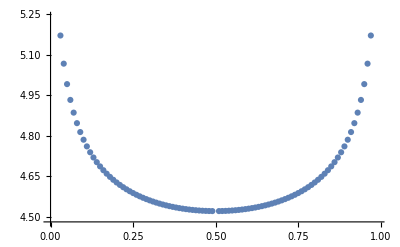

```mathematica
ListPlot[Transpose@{p,tcross}]
```

```mathematica
LargestPole=MapThread[Max,{Pol1,Pol2}];
SmallestPole=MapThread[Min,{Pol1,Pol2}];
```

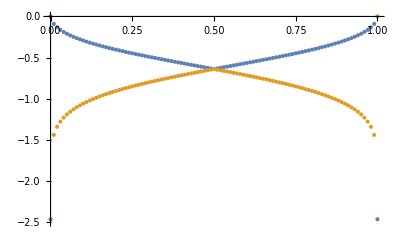

```mathematica
ListPlot[{Prepend[Transpose@{p,LargestPole},{{0,0},{1,0}}],Transpose@{p,SmallestPole},Transpose@{p,Sqrt[r1F1Opt]},Transpose@{p,Sqrt[r2F1Opt]}},PlotRange->{{0,1},{-2.5,0}}]
```

## Appendix C

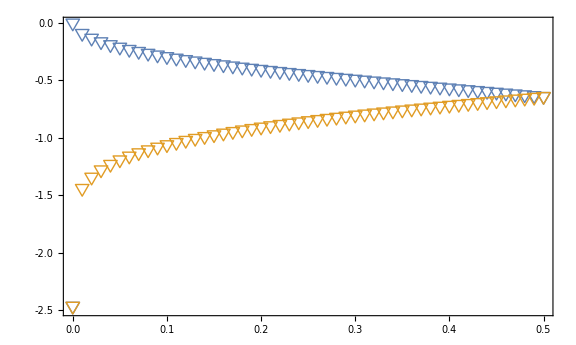

```mathematica
SizeMarker=16;SizeLegend=2;
xm=0;xM=0.5;ym=-2.5;yM=0;Δxm=0.05;ΔxM=0.1;Δym=0.25;ΔyM=0.5;
PolesPlot=Show[ListPlot[{Append[Prepend[Transpose@{p[[;;51]],LargestPole[[;;51]]},{0,0}],{1,0}],Append[Prepend[Transpose@{p[[;;51]],SmallestPole[[;;51]]},{0,LargestPole[[1]]}],{1,Last[LargestPole]}]},PlotRange->{{xm,xM},{ym,yM}},PlotMarkers->{Style["▽",SizeMarker],Style["▽",SizeMarker]},PlotLegends->Placed[{MaTeX["s_+^*",Magnification->SizeLegend],MaTeX["s_-^*",Magnification->SizeLegend]},{0.5,0.3}]],Frame-> True,FrameLabel->{MaTeX["p",Magnification->2],MaTeX["s^*",Magnification->2]},FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],AxesStyle->Directive[Black,10,FontFamily->"Times New Roman",Thickness[0.001]],Method->{"AxesInFront"->False},FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->{0.02,(yM-ym)/15}]
```

```mathematica
Export["/Users/gregarval/Documents/Poles_AppendixD.png",PolesPlot,ImageResolution->1200]
```

/Users/gregarval/Documents/Poles_AppendixD.png